```mathematica
Quit[]
```

```mathematica
ClearAll["`*"]
```

# #3: Stochastic Gravitational Wave Background

## Preamble

```mathematica
SetDirectory[NotebookDirectory[]];
PlotsDir=NotebookDirectory[]<>"results/plots/"
```

/home/buenabad/Documents/codes/git_codes/graphare/results/plots/

```mathematica
$Assumptions=a>0&&x>0&&γ>0&&γi>0&&γd>0&&μ>0&&A>0&&λ>0&&4 A^2<3 λ μ^2&&0<Δ<1&&T>T0>0&&Tc>T0>0&&0<λbar<9/8&&f>1&&vw>0&&mPL>0&&θ>0&&t>0&&Σ>0&&gstar>0&&Arho>0&&k>0&&ϵ>0
```

a>0&&x>0&&γ>0&&γi>0&&γd>0&&μ>0&&A>0&&λ>0&&4 A^2<3 λ μ^2&&0<Δ<1&&T>T0>0&&Tc>T0>0&&0<λbar<9/8&&f>1&&vw>0&&mPL>0&&θ>0&&t>0&&Σ>0&&gstar>0&&Arho>0&&k>0&&ϵ>0

## Definitions

```mathematica
Clear[GeV,MeV,Mpl,mpl,second,Hz,mHz,h,ρcrit,H0,H0h1,Tγ0,gs0,ge0,gSM,Aρ,ρχi]
```

### Units

```mathematica
GeV=1;
MeV=10^-3 GeV;
Mpl=1.22091 10^19 GeV;
mpl=Mpl/√(8π);
second=1.519268 10^21/MeV;
Hz=1/second;
mHz=10^-3 Hz;
```

### Constants

```mathematica
h=0.67;
ρcrit=8.0992*10^-47*h^2 GeV^4;
H0=√(ρcrit/(3 mpl^2));
H0h1=H0/h;

Tγ0=(2.4*10^-4)×10^-9 GeV;
gs0=3.94;
ge0=3.38;
gSM=106.75;
```

### Useful

```mathematica
Aρ=gstar π^2/30;
ρχi=3 Hi^2 mpl^2;
```

## Packages

### InterpolatingFunctionsAnatomy

```mathematica
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
```

### DSReheating

```mathematica
Needs["DSReheating`"]
```

### PhaseTransition

```mathematica
Needs["PhaseTransition`"]
```

### dePrivFn: De-Privatize Function

Changes context from Package`Private` to Global`:

```mathematica
ContextName["PT"]="PhaseTransition`Private`";
ContextName["RH"]="DSReheating`Private`";

PrivateDict["PT"]={μ,A,λ,Δ,λbar,Mc,M,δ,T,Tc,Ts,T0};
PrivateDict["RH"]={x,rχ,rr,Hi,gstar,f,γ,Arho,Tc,mPL};
```

```mathematica
Clear[PrivFn,dePrivRule,dePrivFn]

PrivFn[ctxt_,x_]:=ToExpression[ContextName[ctxt]<>ToString[x]]
dePrivRule[ctxt_]:=dePrivRule[ctxt]=(PrivFn[ctxt,#]->#&/@PrivateDict[ctxt])~Join~(PrivFn[ctxt,PrivFn[ctxt,#]]->#&/@PrivateDict[ctxt]);
dePrivFn[ctxt_,ff_,x___:Null]:=(If[x===Null,If[FailureQ[PrivFn[ctxt,ff]],ff,PrivFn[ctxt,ff]],If[FailureQ[PrivFn[ctxt,ff[x]]],ff[x],PrivFn[ctxt,ff[x]]]])/.dePrivRule[ctxt]
```

Examples:

```mathematica
dePrivFn["PT",Ectwa,λbar]
dePrivFn["PT",EcAn,λbar]
Assuming[9/8>λbar>1,%//Simplify]
dePrivFn["PT",EcAnHot,λbar]
dePrivFn["PT",EcAn,1.1]
```

(2 π (-3+√(9-8 λbar)+4 λbar)^2)/(81 (-1+λbar)^2)

Which[0≤λbar<1,PhaseTransition`Private`EcAnCold[λbar],9/8≥λbar>1,PhaseTransition`Private`EcAnHot[λbar],λbar==1,∞]

(1.64419 (9/8-λbar)^(3/4))/(1-λbar)^2

(1.64419 (9/8-λbar)^(3/4))/(1-λbar)^2

10.3373

```mathematica
dePrivFn["RH",RHDict["solsAn"]["γ<<1","χD"]]
dePrivFn["RH",RHDict["HcVals"]["γ>>1"]]
dePrivFn["RH",RHDict["acRel"]["γ>>1"]]
```

{rχ[x]→(8-2 x (-6+(4+3 x) γ))/(2+3 x)^3,rr[x]→4/5 (-(2 2^(2/3))/(2+3 x)^(8/3)+1/(2+3 x)) γ}

{(√((Arho f^4 Tc^4)/mPL^2))/(√3),(√(Arho Tc^4))/(√3 mPL)}

f

## Import data

GW experiments

```mathematica
GWLISASensitivity=<<data/GWLISASensitivity.m;
GWETSensitivity=<<data/GWETSensitivity.m;
GWBBOSensitivity=<<data/GWBBOSensitivity.m;
GWDECIGOSensitivity=<<data/GWDECIGOSensitivity.m;
```

## For plots

```mathematica
Needs["MaTeX`"];
SetOptions[MaTeX,"Preamble"->{"\\usepackage{amssymb,amsmath,latexsym,amsfonts,amsthm,color}"}]
Clear[fticksR,fticksR2,fticksR3,PrettyExp,PrettyExpR2,fticksRNoLabels,fticksR2NoLabels]
PrettyExp[x_,MAX_:2]:=If[Abs[x]≥MAX,Superscript[10,x],If[x≥0,10^x,10.^x]]
PrettyExpR2[x_,MAX_:2]:=If[Abs[x]>MAX,Superscript[10,2x],If[x≥0,10^x,10.^x]]
(* Axis for Epsilon versus mass: *)
fticksR[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{i*10.^x,"",{.008,0}},{i,2,9}],{1}],{10.^x,PrettyExp[x,AMAX],{.02,0}}],{x,Floor[Log[10,min]],Ceiling[Log[10,max]],1}],1]
(* Axis for Epsilon versus mass, but with y-axis labels only every 2 decades *)
fticksR2[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{If[i≤10,10.^(x+Log[10,i]),10.^(1+x+Log[10,i-10])]," ",{If[i==10,0.02,0.008],0}},{i,2,20}],{1}],{10.^x,PrettyExp[x,AMAX],{.02,0}}],{x,Floor[Log[10,min]],Ceiling[Log[10,max]],2}],1]
(* Axis for Epsilon^2 versus mass *)fticksR3[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{10.^(x+Log[10,i]/2)," ",{.008,0}},{i,2,10}],{1}],{10.^x,PrettyExpR2[x,AMAX],{.02,0}}],{x,Ceiling[Log[10,min]],Floor[Log[10,max]],1/2}],1]
(* Axis for Epsilon^2 versus mass, but with y-axis labels only every 2 decades *)
fticksR4[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{If[i≤10,10.^(x+Log[10,i]/2),10.^(0.5+x+Log[10,i-10]/2)]," ",{If[i==10,0.02,0.008],0}},{i,2,20}],{1}],{10.^x,PrettyExpR2[x,AMAX],{.02,0}}],{x,Ceiling[Log[10,min]],Floor[Log[10,max]],1}],1]

fticksRNoLabels[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{i*10.^x,"",{.008,0}},{i,2,9}],{1}],{10.^x,"",{.02,0}}],{x,Floor[Log[10,min]],Ceiling[Log[10,max]],1}],1]
fticksR2NoLabels[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{10.^(x+Log[10,i]/2)," ",{.008,0}},{i,2,10}],{1}],{10.^x,"",{.02,0}}],{x,Ceiling[Log[10,min]],Floor[Log[10,max]],1/2}],1]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{amssymb,amsmath,latexsym,amsfonts,amsthm,color}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

```mathematica
Clear[SciStr]
SciStr[x_,decimals_:0,latex_:False]:=Block[{X,pref,dex,scstr,string},

X=Log10[x];
dex=Floor[X];
pref=Round[(10^(X-dex))*10^decimals]*10^-decimals;

scstr=If[latex,StringReplace[ToString[StringForm["`1`\\times 10^(`2`)",pref,dex]],"`"->""],StringReplace[ToString[StringForm["`1`×10^(`2`)",pref,dex]],"\`"->""]];

string=If[MemberQ[{-1,0,1},dex],ToString[(Round[x*10^decimals]/10^decimals)//N],scstr];

Return[string]
]
```

## Phase Transition

```mathematica
Clear[μ,Δ,A,λ]
```

```mathematica
$Assumptions=a>0&&x>0&&γ>0&&γi>0&&γd>0&&μ>0&&A>0&&λ>0&&4 A^2<3 λ μ^2&&0<Δ<1&&T>T0>0&&Tc>T0>0&&0<λbar<9/8&&f>1&&vw>0&&mPL>0&&θ>0&&t>0&&Σ>0&&gstar>0&&Arho>0&&k>0&&ϵ>0
```

a>0&&x>0&&γ>0&&γi>0&&γd>0&&μ>0&&A>0&&λ>0&&4 A^2<3 λ μ^2&&0<Δ<1&&T>T0>0&&Tc>T0>0&&0<λbar<9/8&&f>1&&vw>0&&mPL>0&&θ>0&&t>0&&Σ>0&&gstar>0&&Arho>0&&k>0&&ϵ>0

λ̄ in terms of θ=T/T_c:

```mathematica
λbarRule=(((λbar/.dePrivFn["PT",McλbarToCoeffs])/.T->Tc*θ)/.dePrivFn["PT",ARule])//Simplify
```

(-1+Δ+θ^2)/(Δ θ^2)

## Euclidean energy and action

Let us look, for example, at the dimensionless bubble energy (Ē)_c(λ̄)

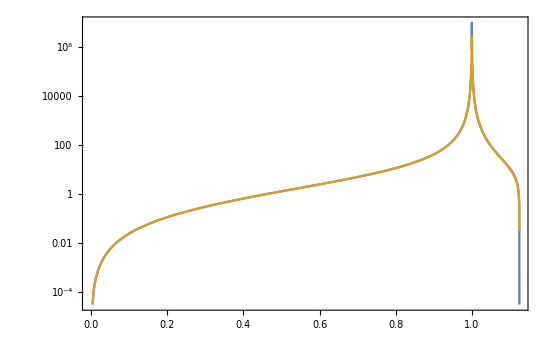

```mathematica
LogPlot[{dePrivFn["PT",EcFn,λbar],dePrivFn["PT",EcAn,λbar]},{λbar,0,9/8},Frame->True]
```

The action is S_E=Φ_b^2/(M T)(Ē)_c. For the exact expression for (Ē)_c(λ̄), let’s plot it as a function of θ=T/T_c for varying Δ parameters:

```mathematica
Clear[μ,Δ,A,λ]

fullSE=(((((dePrivFn["PT",Fb]^2/(dePrivFn["PT",M]*T))*(dePrivFn["PT",EcFn,λbar]/.dePrivFn["PT",McλbarToCoeffs]))/.(dePrivFn["PT",PotToCoeffs]))/.(dePrivFn["PT",ARule]))/.T->Tc*θ)//FullSimplify;
```

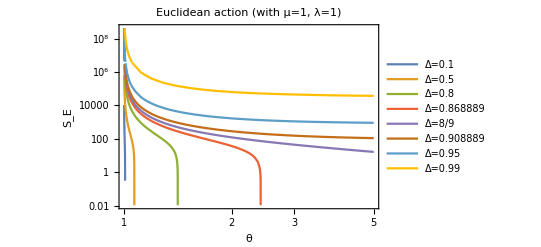

```mathematica
{mu,lam}={1,1};
ΔTab={0.1,0.5,0.8,8/9-0.02,8/9,8/9+0.02,0.95,0.99};
(fullSE/.{μ->mu,λ->lam,Tc->1})//FullSimplify;
(%/.Δ->#&)/@ΔTab;
LogLogPlot[%,{θ,1,5},Frame->True,PlotLegends->(StringForm["Δ=``",#]&/@ΔTab),FrameLabel->{"θ","S_E"},PlotLabel->StringForm["Euclidean action (with μ=`1`, λ=`2`)",mu,lam]]

(*Export[PlotsDir<>"full_SE_theta.pdf",%]*)

Clear[ΔTab,mu,lam]
```

In terms of t=T_c/T:

Power::infy: Infinite expression 1/0.^2 encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity Which[0≤Indeterminate<0.00001,«8»,PhaseTransition`Private`limEcThick[hot][(4 1^2+(3 (Times[«2»]+Times[«2»]) (Times[«2»]+1) 1^2)/Times[«5»]^2)/(4 (1/t)^2)]] encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

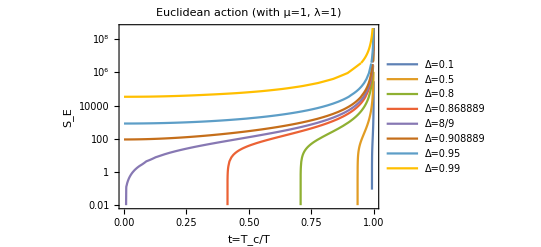

```mathematica
{mu,lam}={1,1};
ΔTab={0.1,0.5,0.8,8/9-0.02,8/9,8/9+0.02,0.95,0.99};
(fullSE/.{μ->mu,λ->lam,Tc->1,θ->1/t})//FullSimplify;
(%/.Δ->#&)/@ΔTab;
LogPlot[%,{t,0,1},Frame->True,PlotLegends->(StringForm["Δ=``",#]&/@ΔTab),FrameLabel->{"t=T_c/T","S_E"},PlotLabel->StringForm["Euclidean action (with μ=`1`, λ=`2`)",mu,lam]]

(*Export[PlotsDir<>"full_SE_t.pdf",%]*)

Clear[ΔTab,mu,lam]
```

Taking the approximate expression instead:

```mathematica
approxSE=Assuming[ll>0,((((((((dePrivFn["PT",Fb]^2/(dePrivFn["PT",M]*T))*(dePrivFn["PT",EcAnHot,λbar]/.dePrivFn["PT",McλbarToCoeffs]))/.(dePrivFn["PT",PotToCoeffs]))/.(dePrivFn["PT",ARule]))/.{T->Tc*θ,λ->ll^2})//FullSimplify)/.Abs[θ]->θ)//FullSimplify)]/.ll->√λ
```

(2.33313 (9+(-8+8/θ^2)/Δ-8/θ^2)^(3/4) θ^3 (1. Δ^(3/2) θ+0.333333 Δ √(8-8 θ^2+Δ (-8+9 θ^2)))^2 μ)/((-1.+Δ)^2 (-1.+θ^2)^2 √(-1+Δ+θ^2) λ)

We can see that as Δ→8/9 the allowed temperatures become larger and larger (i.e. it takes longer to hit the spinodal temperature, or λ̄=9/8). Eventually, once Δ>8/9, a non-zero minimum action is reached.

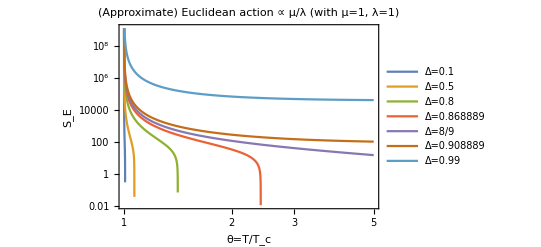

```mathematica
{mu,lam}={1,1};
ΔTab={0.1,0.5,0.8,8/9-0.02,8/9,8/9+0.02,0.99};
(approxSE/.{μ->mu,λ->lam})//FullSimplify;
(%/.Δ->#&)/@ΔTab;
LogLogPlot[%,{θ,1,5},Frame->True,PlotLegends->(StringForm["Δ=``",#]&/@ΔTab),FrameLabel->{"θ=T/T_c","S_E"},PlotLabel->StringForm["(Approximate) Euclidean action ∝ μ/λ (with μ=`1`, λ=`2`)",mu,lam]]

(*Export[PlotsDir<>"approx_SE_theta.pdf",%]*)

Clear[ΔTab,mu,lam]
```

In terms of t=T_c/T:

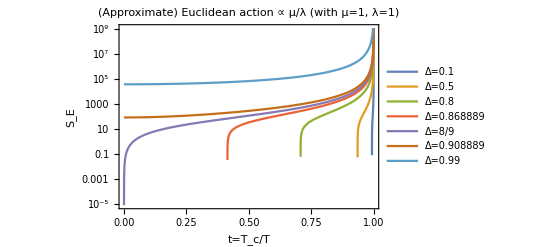

```mathematica
{mu,lam}={1,1};
ΔTab={0.1,0.5,0.8,8/9-0.02,8/9,8/9+0.02,0.99};
Assuming[t>0,(approxSE/.{μ->mu,λ->lam,θ->1/t})//FullSimplify];
(%/.Δ->#&)/@ΔTab;
LogPlot[%,{t,0,1},Frame->True,PlotLegends->(StringForm["Δ=``",#]&/@ΔTab),FrameLabel->{"t=T_c/T","S_E"},PlotLabel->StringForm["(Approximate) Euclidean action ∝ μ/λ (with μ=`1`, λ=`2`)",mu,lam]]

(*Export[PlotsDir<>"approx_SE_t.pdf",%]*)

Clear[ΔTab,mu,lam]
```

## Spinodal temperature

λ̄ will reach 9/8 (corresponding to the spinodal temperature) for some temperature θ as long as Δ<8/9, if Δ≥8/9 then λ̄=9/8 is never reached:

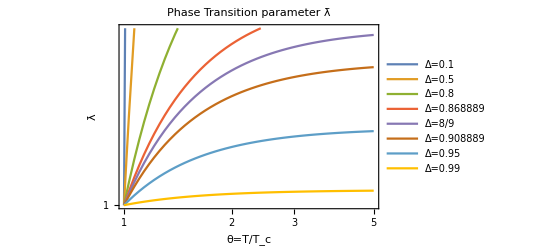

```mathematica
ΔTab={0.1,0.5,0.8,8/9-0.02,8/9,8/9+0.02,0.95,0.99};
(λbarRule/.Δ->#&)/@ΔTab;
LogLogPlot[%,{θ,1,5},Frame->True,PlotLegends->(StringForm["Δ=``",#]&/@ΔTab),FrameLabel->{"θ=T/T_c","λ̄"},PlotRange->{1,9/8},PlotLabel->"Phase Transition parameter λ̄"]
Clear[ΔTab]
```

In terms of t=T_c/T:

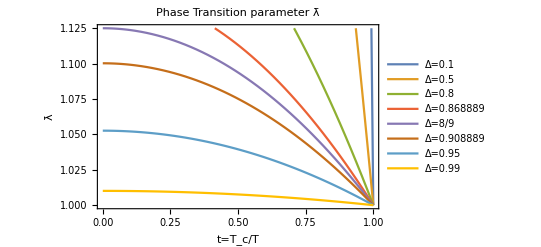

```mathematica
ΔTab={0.1,0.5,0.8,8/9-0.02,8/9,8/9+0.02,0.95,0.99};
((λbarRule/.θ->1/t)/.Δ->#&)/@ΔTab;
Plot[%,{t,0,1},Frame->True,PlotLegends->(StringForm["Δ=``",#]&/@ΔTab),FrameLabel->{"t=T_c/T","λ̄"},PlotRange->{1,9/8},PlotLabel->"Phase Transition parameter λ̄"]

(*Export[PlotsDir<>"lbar_t.pdf",%]*)

Clear[ΔTab]
```

We can then plot Δ(θ) such that λ̄=9/8:

λ̄=(-1+Δ+θ^2)/(Δ θ^2)

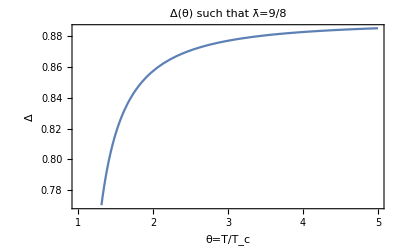

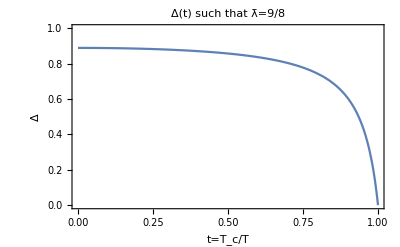

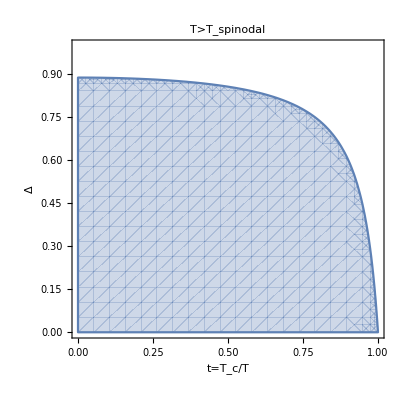

(8 (-1+t^2))/(-9+8 t^2)

```mathematica
lbar=λbarRule;

Print["λ̄=",lbar]
Δ/.(Solve[lbar==9/8,Δ]//Flatten);
Plot[%,{θ,1,5},Frame->True,FrameLabel->{"θ=T/T_c","Δ"},PlotLabel->"Δ(θ) such that λ̄=9/8"]
%%/.θ->1/t;
Plot[%,{t,0,1},Frame->True,FrameLabel->{"t=T_c/T","Δ"},PlotLabel->"Δ(t) such that λ̄=9/8",PlotRange->{{0,1},{0,1}}]

RegionPlot[(lbar/.θ->1/t)>9/8,{t,0,1},{Δ,0,1},FrameLabel->{"t=T_c/T","Δ"},PlotLabel->"T>T_spinodal"]
(*Export[PlotsDir<>"spinodal_t-Delta.pdf",%]*)

(lbar/.θ->1/t)//Simplify;
(Δ/.Solve[%==9/8,Δ]//Flatten)⟦1⟧

Clear[lbar]
```

## Daisy contributions

Daisy contributions from a boson scale like ~N g T, where N is some number associated to the degeneracy of the boson in question. The normal contribution to A scales like ~N g⟨Φ⟩. We then need to compare T/⟨Φ⟩. This factor seems to be irrelevant for most values of Δ as well as for most temperatures, up to and including the spinodal temperature (θ_s=√((8-8Δ)/(8-9Δ))).

The ratio (T/Φ_b)^2 is then given by:

```mathematica
(((((((T/dePrivFn["PT",Fb]/.dePrivFn["PT",PotToCoeffs])/.dePrivFn["PT",TToλbarΔ])/.dePrivFn["PT",ARule])//Simplify//FullSimplify)/.λ->λ^2)//Simplify)/.λ->λ^(1/2))//Simplify;
DaisyRatio=%^2
```

(4 λ)/(3 Δ (3+√(9-8 λbar))^2 μ^2)

(9-8 t^2)/(54-54 t^2)

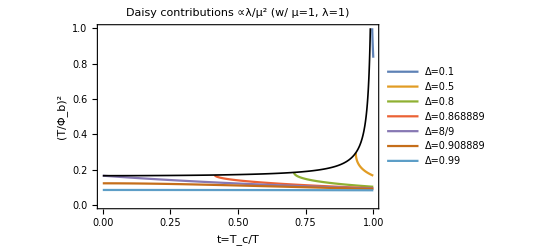

```mathematica
{mu,lam}={1,1};
ΔTab={0.1,0.5,0.8,8/9-0.02,8/9,8/9+0.02,0.99};

daisy=(DaisyRatio/.{λbar->λbarRule})/.{μ->mu,λ->lam,θ->1/t};
Table[daisy,{Δ,ΔTab}];

p1=Plot[%,{t,0,1},Frame->True,PlotLegends->(StringForm["Δ=``",#]&/@ΔTab),FrameLabel->{"t=T_c/T","(T/Φ_b)^2"},PlotRange->{0,1},PlotLabel->StringForm["Daisy contributions ∝λ/μ^2 (w/ μ=`1`, λ=`2`)",mu,lam]];

(Δ/.(Solve[λbarRule==9/8,Δ]//Flatten))/.θ->1/t;
Assuming[t>0,(daisy/.Δ->%)//FullSimplify]
p2=Plot[%,{t,0,1},PlotStyle->{Thickness[0.003],Black},PlotRange->{0,1}];
Show[p1,p2]

(*Export[PlotsDir<>"daisies_t.pdf",%]*)

Clear[ΔTab,daisy,mu,lam,p1,p2]
```

Same as above, but instead plotting the correction to the cubic coefficient (1+(T/Φ_b)^2)^(3/2)-1:

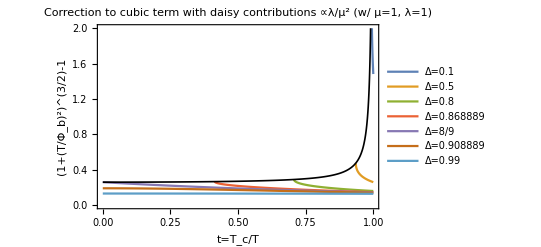

```mathematica
{mu,lam}={1,1};
ΔTab={0.1,0.5,0.8,8/9-0.02,8/9,8/9+0.02,0.99};

daisy=(DaisyRatio/.{λbar->λbarRule})/.{μ->mu,λ->lam,θ->1/t};
Table[(1+daisy)^(3/2)-1,{Δ,ΔTab}];

p1=Plot[%,{t,0,1},Frame->True,PlotLegends->(StringForm["Δ=``",#]&/@ΔTab),FrameLabel->{"t=T_c/T","(1+(T/Φ_b)^2)^(3/2)-1"},PlotRange->{0,2},PlotLabel->StringForm["Correction to cubic term with\ndaisy contributions ∝λ/μ^2 (w/ μ=`1`, λ=`2`)",mu,lam]];

(Δ/.(Solve[λbarRule==9/8,Δ]//Flatten))/.θ->1/t;
Assuming[t>0,(((1+daisy)^(3/2)-1)/.Δ->%)//FullSimplify];
p2=Plot[%,{t,0,1},PlotStyle->{Thickness[0.003],Black},PlotRange->{0,2}];
Show[p1,p2]

(*Export[PlotsDir<>"daisies_t.pdf",%]*)

Clear[ΔTab,daisy,mu,lam,p1,p2]
```

(4 λ)/(3 Δ (3+√(9-8 λbar))^2 μ^2)

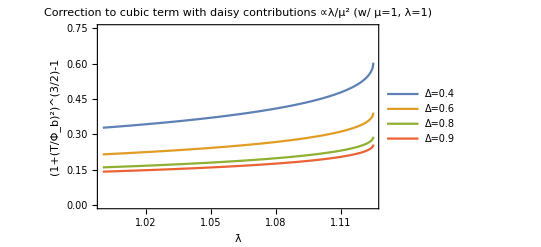

```mathematica
daisy=DaisyRatio

Table[{(1+daisy)^(3/2)-1}/.{λ->1,μ->1},{Δ,{0.4,0.6,0.8,0.9}}];

Plot[%,{λbar,1,9/8},Frame->True,PlotLegends->(StringForm["Δ=``",#]&/@{0.4,0.6,0.8,0.9}),FrameLabel->{"λ̄","(1+(T/Φ_b)^2)^(3/2)-1"},PlotRange->{0,0.75},PlotLabel->StringForm["Correction to cubic term with\ndaisy contributions ∝λ/μ^2 (w/ μ=`1`, λ=`2`)",1,1]]

Clear[daisy]
```

```mathematica
Clear[DaisyRatio]
```

## Runaway condition

The runaway condition is

sign[1-λ̄]((-V_(b,0))-μ^2/2 T^2 Φ_b^2)>0, or alternatively

(-V_(b,0))/(μ^2/2 T^2 Φ_b^2)>1 for λ̄<1 (cPT) .

(-V_(b,0))/(μ^2/2 T^2 Φ_b^2)<1 for λ̄>1 (hPT) .

```mathematica
num=-(dePrivFn["PT",Vb0]/.dePrivFn["PT",PotToCoeffs0Temp])/.dePrivFn["PT",ARule]

den=((((μ^2/2(T*dePrivFn["PT",Fb])^2)/.dePrivFn["PT",PotToCoeffs])/.dePrivFn["PT",ARule])/.dePrivFn["PT",TToλbarΔ])//FullSimplify

condition=num/den
```

(3 Tc^4 (-1+Δ)^2 μ^4)/(2 λ)

(3 Tc^4 (-1+Δ)^2 Δ (9+3 √(9-8 λbar)-4 λbar) μ^4)/(4 λ (-1+Δ λbar)^2)

(2 (-1+Δ λbar)^2)/(Δ (9+3 √(9-8 λbar)-4 λbar))

Runaway for hPT (note that when Δ≥8/9 the condition becomes zero for some λ̄<9/8, for which T→∞ because the spinodal temperature does not exist), and also for cPT.

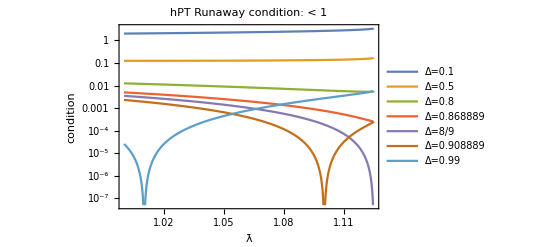

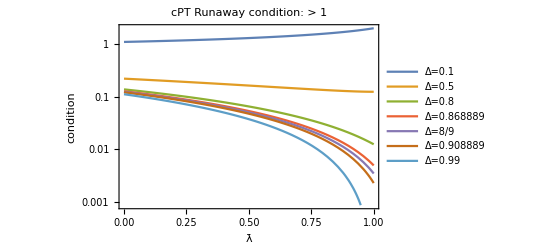

```mathematica
ΔTab={0.1,0.5,0.8,8/9-0.02,8/9,8/9+0.02,0.99};
condition=Table[condition/.Δ->Δval,{Δval,ΔTab}];

LogPlot[condition,{λbar,1,9/8},Frame->True,PlotLegends->(StringForm["Δ=``",#]&/@ΔTab),FrameLabel->{"λ̄","condition"},PlotLabel->"hPT Runaway condition: < 1"]

LogPlot[condition,{λbar,0,1},Frame->True,PlotLegends->(StringForm["Δ=``",#]&/@ΔTab),FrameLabel->{"λ̄","condition"},PlotLabel->"cPT Runaway condition: > 1"]

Clear[num,den,condition,ΔTab,cond]
```

## Clear

```mathematica
(*Clear[λbarRule]*)
```

## Reheating

Exact {x_c1,x_max,x_c2}:

{0.0052046713980030820466111475125,0.533924602438869526295205769273,50.417572695509001287721062276}

Approximate {x_c1,x_max,x_c2}:

{0.00511109,0.534187,52.1741}

Error [(Approx-Exact)/Exact]:

{-0.0179801,0.00049089,0.03484}

Domain:

{0,100000.}

γ_c^RATE

{0.2454826767774449779161,-0.2514731273841883583828}

-Graphics-

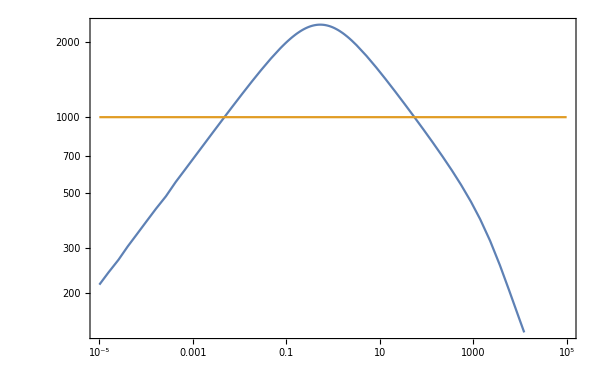

```mathematica
gam=0.001;
regime=If[gam≤1,"γ<<1","γ>>1"];

eff=Max[((*2.5*)2.2*1.7)/gam^(1/4),2];
rcrit=eff^-4;

res=solEqs[gam,0,10^3,40,20];
Print["Exact {x_c1,x_max,x_c2}:"]
xLR=xCross[gam,rcrit]
((dePrivFn["RH",RHDict["xcVals"][regime]])/.{γ->gam,f->eff})//N;
((dePrivFn["RH",RHDict["xMax"][regime]])/.{γ->gam,f->eff})//N;
Print["Approximate {x_c1,x_max,x_c2}:"]
{%%%⟦1⟧,%%,%%%⟦2⟧}
Print["Error [(Approx-Exact)/Exact]:"]
(%%/%%%%%%)-1

Print["Domain:"]
domain=InterpolatingFunctionDomain[res⟦2⟧]//Flatten

Print["γ_c^RATE"]
{gammaRate[gam,xLR⟦1⟧],gammaRate[gam,xLR⟦-1⟧]}

p1=LogLogPlot[{res⟦1⟧[x],res⟦2⟧[x]},{x,10^-5,domain⟦2⟧},PlotRange->{10^-8,100},PlotStyle->{{Blue,Thick},{Red,Thick}},GridLines->{(xLR)~Join~{1/gam},{rcrit}},Frame->True,ImageSize->600,FrameTicks->{{fticksR2[10^-20,10^10,2],fticksRNoLabels[10^-20,10^10,2]},{fticksR[10^-10,10^10,2],fticksRNoLabels[10^-10,10^10,2]}},LabelStyle->16,FrameLabel->{MaTeX["(t-t_i)H_i",Magnification->2],MaTeX["\\rho/\\rho_{\\chi,i}",Magnification->2]},PlotLegends->Placed[LineLegend[{MaTeX["\\rho_{\\chi}",Magnification->1.7],MaTeX["\\rho_{r}",Magnification->1.7]}],{0.9,0.85}],Epilog->{Inset[Rotate[MaTeX["\\color{black} t=t_\\textrm{max}",Magnification->1.5],90°],Scaled[{.43,.2}]],Inset[Rotate[MaTeX["\\color{black} t=\\Gamma_\\chi^{-1}",Magnification->1.5],90°],Scaled[{.63,.2}]],Inset[Rotate[MaTeX["\\color{black} T=T_c",Magnification->1.5],0°],Scaled[{.08,.55}]],Inset[Rotate[MaTeX[ToString["\\begin{aligned} \\Gamma_\\chi &= "<>ToString[gam]<>"H_i \\end{aligned}"],Magnification->1.3],0°],Scaled[{.13,.9}]]}];

χDFns={rχ[x]/.(dePrivFn["RH",RHDict["solsAn"][regime,"χD"]]),rr[x]/.(dePrivFn["RH",RHDict["solsAn"][regime,"χD"]])}/.{γ->gam,f->eff};
RDFns={rχ[x]/.(dePrivFn["RH",RHDict["solsAn"][regime,"RD"]]),rr[x]/.(dePrivFn["RH",RHDict["solsAn"][regime,"RD"]])}/.{γ->gam,f->eff};
(χDFns~Join~RDFns);

p2=LogLogPlot[%,{x,10^-5,domain⟦2⟧},PlotStyle->{{Blue,Dashed,Thickness[0.002]},{Red,Dashed,Thickness[0.002]},{Blue,Dotted,Thickness[0.002]},{Red,Dotted,Thickness[0.002]}},PlotRange->{10^-8,100},Frame->True,ImageSize->600,FrameTicks->{{fticksR2[10^-20,10^10,2],fticksRNoLabels[10^-20,10^10,2]},{fticksR[10^-10,10^10,2],fticksRNoLabels[10^-10,10^10,2]}},LabelStyle->16];

Show[p1,p2]

gSS=10;
TC=1000;
HI=eff^2*(Aρ/.gstar->gSS)*TC^2/(3mpl);
TOfx[gam,gSS,HI,0,10^3,30,20];
LogLogPlot[{%[x],TC},{x,10^-5,domain⟦2⟧},Frame->True,FrameLabel->{MaTeX["(t-t_i)H_i",Magnification->2],MaTeX["T [\\mathrm{GeV}]",Magnification->2]}]

Clear[gam,eff,regime,rcrit,res,xLR,domain,χDFns,RDFns,p1,p2,gSS,TC,HI]
```

## Gravitational Wave Spectra

## Stochastic Gravitational Wave Background from First Order Phase Transition (SGWB from 1PT)

## Analytical Approximations

### Some crude estimates

```mathematica
(Tγ0^4/((10^3)^4))*(((10^3)^4)/ρcrit)
```

0.0000912543

```mathematica
(Tγ0^4/ρcrit)^(1/4)
```

0.097738

```mathematica
((10^3)^(4*2))/(ρcrit Tγ0^4)
```

8.29017×10^120

### a_*

```mathematica
dePrivFn["RH",RHDict["acRel"]["γ<<1"]]
dePrivFn["RH",RHDict["acRel"]["γ>>1"]]
```

If[8 f^2 γ≤15,(1+(2 f^4 γ)/5)^(2/3),(0.904981 f)/γ^(1/6)]

f

#### Test

```mathematica
gDSUV=10;
gVSUV=0.(*106.75*);
gs=gDSUV+gVSUV;

gam=0.1;
regime=If[gam≤1,"γ<<1","γ>>1"];
eff=If[regime=="γ<<1",2.2*(1.7/gam^(1/4)),3.3*(1+1./gam^(1/2))];
Print["γ=",gam,", f=",eff]

solEqs[gam];
{xC1,xMAX,xC2}=xCross[gam,eff^-4]
dePrivFn["RH",RHDict["xcVals"]["γ<<1"]]/.{γ->gam,f->eff}

Tcr=1000GeV;
Hdec=√(eff^4(Aρ Tcr^4)/(3 mpl^2)/.gstar->gs);
Tofx=TOfx[gam,gs,Hdec];
domain=InterpolatingFunctionDomain[Tofx]//Flatten;

redshift[gam,Hdec,{xC1,domain⟦2⟧},{gDSUV,gVSUV},{Automatic,0,gSM},True,0,10^3,30,20,False]
redshift[gam,Hdec,{xC2,domain⟦2⟧},{gDSUV,gVSUV},{Automatic,0,gSM},True,0,10^3,30,20,False]
%%/%

dePrivFn["RH",RHDict["acRel"][regime]]/.{γ->gam,f->eff}

Clear[gDSUV,gVSUV,gs,gam,regime,eff,Tcr,Hdec,Tofx,domain,xC1,xMAX,xC2]
```

γ=0.1, f=6.65076

{0.0052060385975840513743190972669,0.50980670953903534052457302086,22.074185688237547749521517574}

{0.00511109,22.1163}

7.04816×10^16

7.45458×10^15

9.45481

8.83441

### (d S)/(d t), (d^2 S)/(d t)|_max

The most straightforward way to compute these quantities is by using the chain rule

(d S)/(d t)=(d S)/(d lnT)(d lnT)/(d t)=S(d lnS)/(d λ̄)(d λ̄)/(d lnT)(d lnT)/(d t)

(d^2 S)/(d t^2)|_max=((d S)/(d lnT)(d^2 lnT)/(d t^2)+(d^2 S)/(d lnT^2)((d lnT)/(d t))^2)|_max=(d S)/(d lnT)(d^2 lnT)/(d t^2)|_max+0=S(d lnS)/(d λ̄)(d λ̄)/(d lnT)(d^2 lnT)/(d t^2)|_max,

and  S=P_s×(Ē)_c.

```mathematica
newPS=(dePrivFn["PT",PS]/.dePrivFn["PT",ARule])//FullSimplify;

dePrivFn["PT",EcAnCold,λbar]
dePrivFn["PT",EcAnHot,λbar]

dλdlnTAn=((dePrivFn["PT",dλdlnT]/.dePrivFn["PT",TToλbarΔ])/.dePrivFn["PT",ARule])//FullSimplify
```

(1.97649 (1.13088-λbar)^0.914352 λbar^2)/(1-λbar)^2

(1.64419 (9/8-λbar)^(3/4))/(1-λbar)^2

2/Δ-2 λbar

P_S/((μ √Δ)/λ):

(3 (3+√(9-8 λbar))^2)/(4 √λbar)

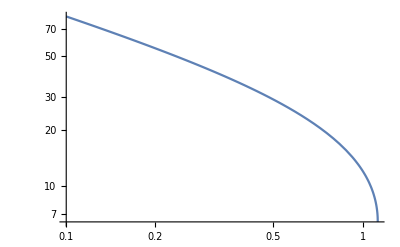

```mathematica
(newPS/((μ √Δ)/λ))//Simplify
LogLogPlot[%,{λbar,0.1,9/8}]
```

(d lnS)/(d λ̄)

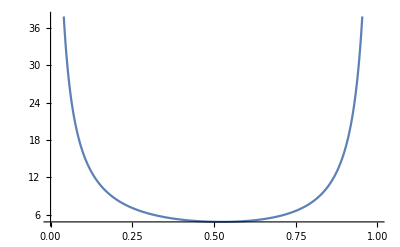

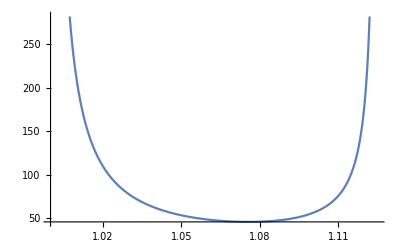

```mathematica
dlnSdλCold=(D[Log[newPS]+Log[dePrivFn["PT",EcAnCold,λbar]],λbar])//Expand//FullSimplify;
Plot[dlnSdλCold,{λbar,0,1}]
dlnSdλHot=(D[Log[newPS]+Log[dePrivFn["PT",EcAnHot,λbar]],λbar])//Expand//FullSimplify;
Plot[dlnSdλHot//Abs,{λbar,1,9/8}]
```

```mathematica
dlnSdλColdEst=D[Log[dePrivFn["PT",SAnColdPL,λbar]],λbar]
dlnSdλHotEst=D[Log[dePrivFn["PT",SAnHotPL,λbar]],λbar]
```

4.85499

-45.609

```mathematica
dλdlnTAn/.λbar->dePrivFn["PT",λbarInfCold]
dλdlnTAn/.λbar->dePrivFn["PT",λbarInfHot]
```

-1.04589+2/Δ

-2.15132+2/Δ

```mathematica
dlnSdlnTAn["cold"]=dlnSdλCold*dλdlnTAn;
dlnSdlnTAn["hot"]=dlnSdλHot*dλdlnTAn;

dlnSdlnTEst["cold"]=dlnSdλColdEst*(dλdlnTAn/.λbar->dePrivFn["PT",λbarInfCold]);
dlnSdlnTEst["hot"]=dlnSdλHotEst*(dλdlnTAn/.λbar->dePrivFn["PT",λbarInfHot]);

dlnSdxAn["hot","γ<<1"]=dePrivFn["RH",RHDict["LrcVals"]["γ<<1"]]⟦1⟧dlnSdlnTAn["hot"];
dlnSdxAn["cold","γ<<1"]=dePrivFn["RH",RHDict["LrcVals"]["γ<<1"]]⟦2⟧dlnSdlnTAn["cold"];

dlnSdxAn["hot","γ>>1"]=dePrivFn["RH",RHDict["LrcVals"]["γ>>1"]]⟦1⟧dlnSdlnTAn["hot"];
dlnSdxAn["cold","γ>>1"]=dePrivFn["RH",RHDict["LrcVals"]["γ>>1"]]⟦2⟧dlnSdlnTAn["cold"];

d2lnSdx2An["hot","γ<<1"]=dePrivFn["RH",RHDict["L2rrMax"]["γ<<1"]]dlnSdlnTAn["hot"];
d2lnSdx2An["hot","γ>>1"]=dePrivFn["RH",RHDict["L2rrMax"]["γ>>1"]]dlnSdlnTAn["hot"];
```

```mathematica
?dlnSdλCold
```

```mathematica
?dlnSdλHot
```

```mathematica
?dλdlnTAn
```

```mathematica
?dlnSdlnTAn
```

```mathematica
?dlnSdxAn
```

```mathematica
?d2lnSdx2An
```

## Numeric SGWB

### SGWB spectra formulas

```mathematica
Clear[fenv,Senvf,Ωenv,fsw,Sswf,Ωsw,fturb,fturb,Sturbf,Ωturb,κFn]

(*GW from envelope approximation*)
fenv[β_,vw_]:=Abs[β](0.62/(1.8-0.1vw+vw^2))*GeV/mHz(*[mHz]*);
Senvf[f_,fenv_]:=(3.8 (f/fenv)^2.8)/(1+2.8(f/fenv)^3.8);
Ωenv[f_,β_,vw_,R_,κ_,α_,Hs_,Z_,hh_:h]:=Z^-4(Hs/(H0h1*hh))^2*R^2((κ α)/(1+α))^2*(Hs/β)^2((0.11 vw^3)/(0.42+vw^2))Senvf[f,Z^-1 fenv[β,vw]];

(*GW from sound waves*)
fsw[β_,vw_]:=2/(√3)×β/vw*GeV/mHz(*[mHz]*);
Sswf[f_,fsw_]:=(f/fsw)^3(7/(4+3(f/fsw)^2))^(7/2)
Ωsw[f_,β_,vw_,R_,κ_,α_,Hs_,Z_,hh_:h]:=Z^-4(Hs/(H0h1*hh))^2*0.159*R^2((κ α)/(1+α))^2*(Hs/β)vw Sswf[f,Z^-1 fsw[β,vw]];

(*GW from turbulence*)
fturb[β_,vw_]:=3.5/2×β/vw*GeV/mHz(*[mHz]*);
Sturbf[f_,fturb_,hstar_]:=(f/fturb)^3/((1+f/fturb)^(11/3)(1+8π f/hstar))
Ωturb[f_,β_,vw_,R_,κ_,α_,Hs_,Z_,hh_:h]:=Z^-4(Hs/(H0h1*hh))^2*20.1*R^2((κ α)/(1+α))^2*(Hs/β)vw Sturbf[f,Z^-1 fturb[β,vw],Z^-1 Hs*GeV/mHz];

(*efficiency*)
κFn[vw_,αN_]:=Block[{αn=αN,αmax,α,cs,vwJ,κA,κB,κC,κD,δκ},

αmax=1/3(1-vw)^(-13/10);
α=Min[αN,αmax];
cs=√(1/3);
vwJ=1/(1+α)(√(2/3 α+α^2)+√(1/3));
κA=vw^(6/5)(6.9α)/(1.36-0.037 √α+α);
κB=α^(2/5)/(0.017+(0.997+α)^(2/5));
κC=(√α)/(0.135+√(0.98+α));
κD=α/(0.73+0.083 √α+α);
δκ=-0.9Log[(√α)/(1+√α)];

If[0≤vw≤cs,
(cs^(11/5)κA κB)/((cs^(11/5)-vw^(11/5))κB+vw cs^(6/5)κA),
If[cs<vw<vwJ,
κB+(vw-cs)δκ+(vw-cs)^3/(vwJ-cs)^3(κC-κB-(vw-cs)δκ),
If[vwJ≤vw≤1,
((vwJ-1)^3 vwJ^(5/2)vw^(-5/2)κC κD)/(((vwJ-1)^3-(vw-1)^3)vwJ^(5/2)κC+(vw-1)^3 κD),
Print["Error"]
]
]
]
];
```

### Numeric SGWB from 1PT

```mathematica
Clear[gwSpectra]

gwSpectra[gUVs_List,vwCool_,coeffs_List,Tcrit_,Hd_,Γχ_,method_,verbose_:False,hh_:h,KfacΓfull_List:{1,False},NlxExpansionSum_List:{250,False,True},IRinstantVSRHwx_List:{Automatic,0,gSM,True,0},δxLargePrecAccu_List:{10^-6,10^10,30,20}]:=gwSpectra[gUVs,vwCool,coeffs,Tcrit,Hd,Γχ,method,verbose,hh,KfacΓfull,NlxExpansionSum,IRinstantVSRHwx,δxLargePrecAccu]=Block[{gdUV,gUV,gstar,Tc=Tcrit,Hi=Hd,γd=Γχ/Hd,Kfactor,full,Nlx,expansion,sum,wχ,gdIR,gd0,gIR,instantVSRH,δ,xLarge,prec,accu,xd,t0,rχ,rr,Tx,ax,tx,xDomain,xm,rCrit,xCritBoil,xpk,xCritCool,Tpk,xcs,tcs,TempEvol,gammas,vwboil=1,Tpts,tpts,λbars,Φbs,ϵs,Ecs,SEs,S1s,S2s,ΓVs,β1s,β2s,nbs,Rbs,Ravgs,βeffs,α∞s,αns,effs,xpts,Hss,Rs,Zs, fullResult,fullResultLabels,spec,tmp},

(*distributing list arguments*)
{gdUV,gUV}=gUVs(*DS & VS UV d.o.f.*);
gstar=gdUV+gUV(*total plasma UV d.o.f.*);

{Kfactor,full}=KfacΓfull(*K-prefactor for Subscript[Γ, nucl]/𝒱; whether (Subscript[S, E]/2π)^(3/2) 0-modes prefactor included*);

{Nlx,expansion,sum}=NlxExpansionSum(* # ln(x) steps; whether Universe expansion considered; whether sum for a(x) and τ̄(x) considered*);

{gdIR,gd0,gIR,instantVSRH,wχ}=IRinstantVSRHwx(*DS d.o.f. in IR; DS-to-VS temperature ratio in IR; VS d.o.f. in IR, VS temperature in IR; whether VS reheated instantaneously; reheaton e.o.s.*);
gdIR=If[gdIR===Automatic,gdUV,gdIR];

{δ,xLarge,prec,accu}=δxLargePrecAccu(*tiny number for derivative computation, largest x-value for reheating story, precision, accuracy*);

(*the reference time, at which the χ-decays start*)
tmp=dePrivFn["RH",xd];
xd=tmp;
t0=xd/Hi;

(*the solutions to the reheating equations*)
{rχ,rr}=solEqs[γd,wχ,xLarge,prec,accu];

(*T(x)*)
Tx=TOfx[γd,gstar,Hi,wχ,xLarge,prec,accu];

(*scale factor a(x), with Subscript[a, ini]=a(x=Subscript[x, d])=1*)
ax=If[expansion==False,1,aOfx[γd,1,sum,wχ,xLarge,prec,accu]];

(*dimensionless comoving time τ̄(x)*)
tx=If[expansion==False,1,tauOfx[γd,1,1,sum,wχ,xLarge,prec,accu]];

(*its time domain*)
xDomain=(InterpolatingFunctionDomain[Tx]//Flatten);

(*deep in DS RD*)
xm=xDomain⟦-1⟧;

(*the dimensionless radiation density at critical temperature*)
rCrit=(Aρ Tc^4)/ρχi;

(*the dimensionless crossing times, at which the radiation density reaches critical temperature*)
{xCritBoil,xpk,xCritCool}=xCross[γd,rCrit,wχ,xLarge,prec,accu];

(*the peak temperature*)
Tpk=Tx[xpk];

(*a handy list for dimensionless crossing times*)
xcs={xCritBoil,xCritCool};

(*the dimensionful critical times*)
tcs=xcs/Hi;

(*reading 'method' argument to find PT temperature*)
If[MemberQ[{"analytic","semi","numeric","alt"},method]==False,Return["Please write argument 'method' a string: either 'analytic', 'semi', 'numeric', or 'alt'."]];

(*computing the PT*)
If[method=="analytic",
(*the power law behavior of the temperature as a function of time*)
gammas=gammaRate[γd,#,wχ,δ,xLarge,prec,accu]&/@xcs;
(*the parameters for the temperature evolution*)
TempEvol=Table[{gammas⟦i⟧,t0,tcs⟦i⟧},{i,2}];
,
(*the arguments for the temperature evolution*)
TempEvol={Tx,1/Hi}&/@{_,_}(*making a copy: for boiling and cooling*);
];

(*finding the properties of the phase transition: a list of pairs; the first entry being the boiling PT, the second the cooling PT*)
(*{Subscript[T, PT], Subscript[t, PT], λ̄, Subscript[Φ, b], ϵ, Subscript[E, c], Subscript[S, E], Subscript[S, E]', Subscript[S, E]'', Subscript[Γ, nucl]/𝒱, Subscript[β, 1], Subscript[β, 2], Subscript[n, b], Subscript[R, b], <R>, Subscript[β, eff], Subscript[α, ∞], Subscript[α, n], Subscript[κ, run]}*)
{Tpts,tpts,λbars,Φbs,ϵs,Ecs,SEs,S1s,S2s,ΓVs,β1s,β2s,nbs,Rbs,Ravgs,βeffs,α∞s,αns,effs}={CheckAbort[ptParams[gstar,"hot",vwboil,TempEvol⟦1⟧,coeffs,Tcrit,method,Kfactor,full,{ax,tx},Nlx],Table[0,19]],
CheckAbort[ptParams[gstar,"cold",vwCool,TempEvol⟦2⟧,coeffs,Tcrit,method,Kfactor,full,{ax,tx},Nlx],Table[0,19]]}//Transpose;

(*dimensionless times at which the PT took place*)
xpts=tpts*Hi;

(*Hubble scale at the time of GW generation, which we take to be the time of the PT: H_*=Subscript[H, PT]*)
Hss=Hi*√(rχ[#]+rr[#])&/@xpts;

(*correction due to Subscript[ρ, tot] containing a contribution from the reheaton and not only the DS radiation*)
Rs=Table[((1+αns⟦i⟧)/(1+rχ[xpts⟦i⟧]/rr[xpts⟦i⟧])),{i,2}];

(*the extra redshift factor that GW from boiling PT undergo compared to those from cooling PT*)
Zs=redshift[γd,Hi,{#,xm},{gdUV,gUV},{gdIR,gd0,gIR},instantVSRH,wχ,xLarge,prec,accu,False]&/@xpts;

fullResult={xpk/Hi,xpk,Tpk,tcs,xcs,Tpts,tpts,tpts*Hi,λbars,Φbs,ϵs,Ecs,SEs,S1s,S2s,ΓVs,β1s,β2s,nbs,Rbs,Ravgs,βeffs,α∞s,αns,effs,Hss,Rs,Zs};
fullResultLabels={"t_max=``","x_max=``","T_max=``","t_c=``","x_c=``","T_PT=``","t_PT=``","x_PT=``","λ̄=``","Φ_b=``","ϵ=``","E_c=``","S_E=``","S_E'=``","S_E''=``","Γ/V=``","β_1=``","β_2=``","n_b=``","R_b=``","⟨R⟩=``","β_eff=``","α_∞=``","α_n=``","κ_eff=``","H_*=``","R=``","Z=``"};

(*print the quantities above*)
If[verbose,Print[StringRiffle[Table[StringForm[fullResultLabels⟦i⟧,ScientificForm[fullResult⟦i⟧,4]],{i,Length@fullResult}],"\n"]]];

spec={Ωenv[f,βeffs⟦1⟧,vwboil,Rs⟦1⟧,effs⟦1⟧,αns⟦1⟧,Hss⟦1⟧,Zs⟦1⟧,hh],Ωsw[f,βeffs⟦2⟧,vwCool,Rs⟦2⟧,κFn[vwCool,αns⟦2⟧],αns⟦2⟧,Hss⟦2⟧,Zs⟦2⟧,hh]};

Return[spec]
]
```

### Examples

Some examples of parameters that work:

1. g_s=10, v_w^c=0.05, {μ, Δ, λ}={2,0.5, 1}, T_c=500 GeV (—5 TeV), γ=0.2, f=(1.03×1.7/γ^(1/4))
2. g_s=10, v_w^c=0.05, {μ, Δ, λ}={2,0.8, 1}, T_c=200 GeV, γ=0.2 (0.3), f=(1.3×1.7/γ^(1/4))
3. g_s=10, v_w^c=0.05, {μ, Δ, λ}={1.1,0.90889, 1.1}, T_c=5 TeV, γ=0.3, f=(3.7×1.7/γ^(1/4))
4. g_s=10, v_w^c=0.05, {μ, Δ, λ}={1.5,0.888789, 1}, T_c=5 TeV, γ=0.02, f=(2.2×1.7/γ^(1/4))
5. g_s=10, v_w^c=0.05, {μ, Δ, λ}={1, 0.90889, 1}, T_c=500 GeV (—5 TeV), γ=50, f = 3.5*(1+1/γ^(1/2))

#### Parameters

{μ,A,λ}={1,0.75,1}

T_c exists: True

γ=50, f=3.76669

H_i=6.10077×10^-12 GeV

T_c=1000 GeV

T_max=3529.57 GeV ≈ 3486.83 GeV

T_1=1264.91 GeV

T_0=500. GeV

T_c/T_max=0.283321

{x_c1,x_max,x_c2}={0.0000996,0.0544923,6.59903}

λ̄(T_max)=1.30658≈1.30592: T_1 is reached, at x_1=0.0002562

hPT should occur during x∈{0.0000996,0.0002562}

cPT should occur during x∈{6.59903,27.881}

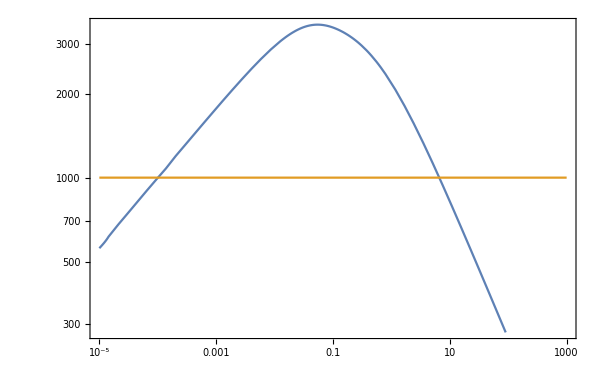

```mathematica
verbose=True;
gDSUV=10;
gVSUV=0.(*106.75*);
gs=gDSUV+gVSUV;
vwc=0.05;

(*
(*VERY STRONG 1PT: Subscript[α, n]>1 ⇒ vacuum energy is important ⇒ evolution during RH is suspect*)
μ=10;
λ=3;*)
μ=1;
λ=1;
(*Δ=8/9+0.01;*)
(*Δ=8./9+0.0001;*)
(*Δ=0.95;*)
(*Δ=8/9-0.0001;*)
(*Δ=0.89;*)
(*Δ=0.85;*)
Δ=0.75;
(*Δ=0.5;*)
A=(A/.(dePrivFn["PT",ARule]));
pars={μ,A,λ};
Print["{μ,A,λ}=",pars]
Print["T_c exists: ",dePrivFn["PT",cond1,pars⟦1⟧,pars⟦2⟧,pars⟦3⟧]]

Tcr=1000GeV;

gam=50;
regime=If[gam≤1,"γ<<1","γ>>1"];
(*Print["f∈[",((dePrivFn["RH",RHDict["fmin"][regime]])/.γ->gam)//N,", ",(fMax[regime]/.γ->gam)//N,"]"]*)
eff=If[regime=="γ<<1",2.2*(1.7/gam^(1/4)),3.3*(1+1./gam^(1/2))];
Print["γ=",gam,", f=",eff]

solEqs[gam];

Hdec=√(eff^4(Aρ Tcr^4)/(3 mpl^2)/.gstar->gs);Gam=gam*Hdec;

Tofx=TOfx[Gam/Hdec,gs,Hdec];
Hofx=HOfx[Gam/Hdec,Hdec];
dlnTdt[x_]=Hdec*D[Tofx[x],x]/Tofx[x];
d2lnTdt2[x_]=Hdec*D[dlnTdt[x],x];

domain=InterpolatingFunctionDomain[Tofx]//Flatten;
{xC1,xMAX,xC2}=xCross[Gam/Hdec,eff^-4];
Tmx=Tofx[xMAX];

Tspin=(Ts/.dePrivFn["PT",Tspinodal])/.Tc->Tcr;
Tbin=(T0/.dePrivFn["PT",Tbinodal])/.Tc->Tcr;

Print["H_i=",Hdec, " GeV"]
Print["T_c=",Tcr, " GeV"]
Print["T_max=",Tmx," GeV ≈ ",(Tcr*(dePrivFn["RH",RHDict["rrMax"][regime]]*f^4)^(1/4)/.{f->eff,γ->gam})," GeV"]
Print["T_1=",Tspin, " GeV"]
Print["T_0=",Tbin, " GeV"]
Print["T_c/T_max=",Tcr/Tmx]

RoundScale=10^(Floor[Log10[xC1]]-2)//N;

Print["{x_c1,x_max,x_c2}=",Round[#,RoundScale]&/@{xC1,xMAX,xC2}]

FullRegime=If[(Δ≥8/9)||(Tspin>Tmx),True,False];
xRangeHot=If[FullRegime,{xC1,xC2},{xC1,xCross[Gam/Hdec,(Tspin/Tcr)^4 eff^-4]⟦1⟧}];
xRangeCold={xC2,xCross[Gam/Hdec,(Tbin/Tcr)^4 eff^-4]⟦3⟧};

λMax=λbarRule/.θ->Tmx/Tcr;
λMaxAppx=λbarRule/.θ->((dePrivFn["RH",RHDict["rrMax"][regime]]*f^4)^(1/4)/.{f->eff,γ->gam});

Print["λ̄(T_max)=",λMax,"≈",λMaxAppx,If[λMax<9/8,": T_1 is never reached",StringForm[": T_1 is reached, at x_1=``",Round[xRangeHot⟦2⟧,RoundScale]]]]

Print["hPT should occur during x∈",Round[#,RoundScale]&/@xRangeHot]
Print["cPT should occur during x∈",Round[#,RoundScale]&/@xRangeCold]


LogLogPlot[{Tofx[x],Tcr},{x,10^-5,domain⟦-1⟧},Frame->True,ImageSize->600,FrameTicks->{{fticksR2[10^-20,10^10,2],fticksRNoLabels[10^-20,10^10,2]},{fticksR[10^-10,10^10,2],fticksRNoLabels[10^-10,10^10,2]}},LabelStyle->16,FrameLabel->{MaTeX["(t-t_i)H_i",Magnification->2],MaTeX["\\mathrm{Temperature}\\ [\\mathrm{GeV}]",Magnification->2]},PlotLegends->Placed[LineLegend[{MaTeX["T_\\mathrm{rh}(x)",Magnification->1.7],MaTeX["T_\\mathrm{c}",Magnification->1.7]}],{0.9,0.85}]]
```

#### PT quantities

TODO:
1. finish notebook, including verbosity
2. check various instances to see if it works

```mathematica
Include0Modes=True;
Print["We shall ",If[Include0Modes,"INCLUDE 0-modes","IGNORE 0-modes"]]
Print[""]

(*nucleation time*)
xn={(x/.FindRoot[Γnucl[pars,Tcr,Tofx[x],1,Include0Modes,True]-4Log10[Hofx[x]]==0,{x,GeometricMean[xRangeHot],xRangeHot⟦1⟧,xRangeHot⟦2⟧}]),(x/.FindRoot[Γnucl[pars,Tcr,Tofx[x],1,Include0Modes,True]-4Log10[Hofx[x]]==0,{x,GeometricMean[xRangeCold],xRangeCold⟦1⟧,xRangeCold⟦2⟧}])};
Tn=Tofx[#]&/@xn;
λn=λbarRule/.θ->#/Tcr&/@Tn;
Sn=SETemp[pars,Tcr,#]&/@Tn;

(*Simultaneous Regime if Γ/𝒱|_max<Subscript[H, max]^4 or if Subscript[x, n] is within 1 order of magnitude of xMAX*)
SimRegime=(FullRegime&&((Γnucl[pars,Tcr,Tmx,1,Include0Modes,True]≤4Log10[Hofx[xMAX]])||(xMAX/xn⟦1⟧ < 10)));

Print["**********************"]
Print["~~~ hPT ~~~"]
Print["..................."]
Print["Nucleation time (when Γ/𝒱=H^4)"]
Print["Γ/𝒱=H_n^4=",Hofx[xn⟦1⟧]^4]
Print["x_n=",xn⟦1⟧,", T_n=",Tn⟦1⟧,", λ̄=",λn⟦1⟧]
Print["S_n=",Sn⟦1⟧,", 4×ln[T_c/H_c]=",4Log[Tcr/Hofx[xC1]]]

Print["..................."]
Print["Percolation time (when h(t_PT)=1/e)"]
{Tpt,tpt,λbarr,Fbb,epss,Ecr,SEu,SE1,SE2,GV,b1,b2,nbub,Rbb,Ravg,beff,alinf,aln,kappaeff}=ptParams[gs,"hot",1,{Tofx,1/Hdec},pars,Tcr,"numeric",1,Include0Modes,{1,1},250];
Print["x_hPT=",tpt*Hdec,", T_hPT=",Tpt,", (λ̄)_hPT=",λbarr]
Print["S_hPT=",SEu]
Print["Γ/𝒱|_hPT=",GV]
Print["β_hPT=",beff]
(*S1Rate[dlnTdt[xn⟦1⟧],pars,Tcr,Tn⟦1⟧](*S'|_hPT*)
beff/SEu(*dlnS/dt|_hPT*)
S1Rate[dlnTdt[xn⟦1⟧],pars,Tcr,Tn⟦1⟧]/Sn⟦1⟧(*dlnS/dt|_n*)*)

If[SimRegime,
SEMax=SETemp[pars,Tcr,Tmx];
SE2Max=S2Rate[dlnTdt[xMAX],d2lnTdt2[xMAX],pars,Tcr,Tmx];
GVMax=(Γnucl[pars,Tcr,Tofx[xMAX],1,Include0Modes]);
n0=(√(2π))/(√SE2Max)GVMax;
dSdlnTMax=dePrivFn["PT",dSdlnT,pars,Tcr,Tmx];

GVMaxAppx=Tmx^4(SEMaxAppx/(2π))^(3/2)Exp[-SEMaxAppx];
SEMaxAppx=dePrivFn["PT",SAn,λMaxAppx];
SE2MaxAppx=SEMaxAppx*Hdec^2*d2lnSdx2An["hot",regime]/.{f->eff,γ->gam,λbar->λMaxAppx};
n0Appx=(√(2π))/(√SE2MaxAppx)GVMaxAppx;
Print["------------------"];
Print["Simultaneous Nucleation"];
Print["------------------"];
Print["(λ̄)_max=",λMax];
Print["S(t_max)=",SEMax];
Print["Γ/𝒱|_max=",GVMax];
Print["S''(t_max)=",SE2Max];
Print["____________"];
Print["Analytic approximation"];
Print["n_(0, an)=",n0];
Print["β_an=(8π n_0)^(1/3)v_w=",(8π n0)^(1/3)];
Print["____________"];
Print["Simple estimate"];
Print["(λ̄)_max≈",λMaxAppx];
Print["S(t_max)≈",SEMaxAppx];
Print["Γ/𝒱|_max≈",GVMaxAppx];
Print["S''(t_max)≈",SEMaxAppx*Hdec^2*d2lnSdx2An["hot",regime]/.{f->eff,γ->gam,λbar->λMaxAppx}];
Print["n_(0, an)≈n_(0, est)=",n0Appx];
Print["β_an≈β_est=(8π n_(0, est))^(1/3)v_w≈",(8π n0Appx)^(1/3)];,

Print["------------------"];
Print["Exponential Nucleation"];
Print["------------------"];
Print["____________"];
Print["Analytic approximation"];
Print["β_an=-S'(t_hPT)=-S_hPT(d lnS)/(d t)|_hPT=",-S1Rate[dlnTdt[tpt*Hdec],pars,Tcr,Tpt]];
Print["____________"];
Print["Simple estimate"];
Print["β_an≈β_est=-S_n(d lnS)/(d lnT)|_((λ̄)_inf)*(d lnT)/(d t)|_x_c1=",-Sn⟦1⟧*dlnSdlnTEst["hot"]*(Hdec*dePrivFn["RH",RHDict["LrcVals"][regime]]⟦1⟧/.{f->eff,γ->gam})];
]


Print[""]
Print["**********************"]
Print["~~~ cPT ~~~"]
Print["..................."]
Print["Nucleation time (when Γ/𝒱=H^4)"]
Print["Γ/𝒱_n=H_n^4=",Hofx[xn⟦2⟧]^4]
Print["x_n=",xn⟦2⟧,", T_n=",Tn⟦2⟧,", λ̄=",λn⟦2⟧]
Print["S_n=",Sn⟦2⟧,", 4×ln[T_c/H_c]=",4Log[Tcr/Hofx[xC2]]]

Print["..................."]
Print["Percolation time (when h(t_PT)=1/e)"]
{Tpt,tpt,λbarr,Fbb,epss,Ecr,SEu,SE1,SE2,GV,b1,b2,nbub,Rbb,Ravg,beff,alinf,aln,kappaeff}=ptParams[gs,"cold",1,{Tofx,1/Hdec},pars,Tcr,"numeric",1,Include0Modes,{1,1},250];

Print["x_cPT=",tpt*Hdec,", T_cPT=",Tpt,", (λ̄)_hPT=",λbarr]
Print["S_cPT=",SEu]
Print["Γ/𝒱|_cPT=",GV]
Print["β_cPT=",beff]
(*S1Rate[dlnTdt[xn⟦2⟧],pars,Tcr,Tn⟦2⟧](*S'|_cPT*)
beff/SEu(*dlnS/dt|_cPT*)
S1Rate[dlnTdt[xn⟦2⟧],pars,Tcr,Tn⟦2⟧]/Sn⟦2⟧(*dlnS/dt|_n*)*)
Print["------------------"];
Print["Exponential Nucleation"];
Print["------------------"];
Print["____________"];
Print["Analytic approximation"]
Print["β_an=-S'(t_cPT)=-S_cPT(d lnS)/(d t)|_cPT=",-S1Rate[dlnTdt[tpt*Hdec],pars,Tcr,Tpt]]
Print["____________"];
Print["Simple estimates"]
Print["β_an≈β_est=-S_n(d lnS)/(d lnT)|_((λ̄)_inf)*(d lnT)/(d t)|_x_c2=",-Sn⟦2⟧*(dlnSdlnTEst["cold"])*(Hdec*dePrivFn["RH",RHDict["LrcVals"][regime]]⟦2⟧/.{f->eff,γ->gam})]

(*Clear[xn,Tn,λn,Sn]*)
```

We shall INCLUDE 0-modes

**********************

~~~ hPT ~~~

...................

Nucleation time (when Γ/𝒱=H^4)

Γ/𝒱=H_n^4=1.38374×10^-45

x_n=0.000185988, T_n=1169.39, λ̄=1.08957

S_n=136.162, 4×ln[T_c/H_c]=130.922

...................

Percolation time (when h(t_PT)=1/e)

x_hPT=0.000203758, T_hPT=1196.31, (λ̄)_hPT=1.10042

S_hPT=79.8187

Γ/𝒱|_hPT=2.00654×10^-21

β_hPT=0.0000129523

------------------

Exponential Nucleation

------------------

____________

Analytic approximation

β_an=-S'(t_hPT)=-S_hPT(d lnS)/(d t)|_hPT=0.0000148105

____________

Simple estimate

β_an≈β_est=-S_n(d lnS)/(d lnT)|_((λ̄)_inf)*(d lnT)/(d t)|_x_c1=0.0000491294

**********************

~~~ cPT ~~~

...................

Nucleation time (when Γ/𝒱=H^4)

Γ/𝒱_n=H_n^4=4.37275×10^-51

x_n=11.3673, T_n=773.325, λ̄=0.775949

S_n=147.291, 4×ln[T_c/H_c]=141.531

...................

Percolation time (when h(t_PT)=1/e)

x_cPT=11.9314, T_cPT=755.566, (λ̄)_hPT=0.749439

S_cPT=122.914

Γ/𝒱|_cPT=1.17304×10^-40

β_cPT=1.92236×10^-10

------------------

Exponential Nucleation

------------------

____________

Analytic approximation

β_an=-S'(t_cPT)=-S_cPT(d lnS)/(d t)|_cPT=2.30205×10^-10

____________

Simple estimates

β_an≈β_est=-S_n(d lnS)/(d lnT)|_((λ̄)_inf)*(d lnT)/(d t)|_x_c2=4.98371×10^-10

```mathematica
(5.193*10^15)^(1/4)
```

8488.96

```mathematica
12746.794424196196^4/(5.193*10^15)
eff
```

5.08377

3.76669

```mathematica
dePrivFn["PT",SAnHotPL,1.1]
```

81.6868

```mathematica
Log[8.*π*0.05^3]
```

-5.76303

```mathematica
12746.794424196196/8488.961826795186
```

1.50157

```mathematica
(1/12746.794424196196*0.000012952327010199002)/(1/((5.193*10^15)^(1/4))*1.9223636701472294*^-10)
```

44871.

```mathematica
dePrivFn["RH",RHDict["acRel"]["γ>>1"]]/.{γ->gam,f->eff}
```

3.76669

```mathematica
regime
```

γ>>1

```mathematica
4Log[-136*dlnSdlnTEst["hot"]*(Hdec*dePrivFn["RH",RHDict["LrcVals"][regime]]⟦1⟧/.{f->eff,γ->gam})]
```

-39.689

```mathematica
dlnSdlnTEst["hot"]
```

-23.5044

```mathematica
(eff^4*gam)/(4*(1169.3879492612748/Tcr)^4)
%^-1
```

1345.6

0.000743164

```mathematica
Log[8.*π*0.05^3]
```

-5.76303

```mathematica
4Log[80./136]+Log[8.*π]
```

1.10166

```mathematica
1/4*1/0.0001859877206968459
```

1344.17

```mathematica
136+4*Log[4*0.0001859877206968459]-4Log[Abs[136*dlnSdlnTEst["hot"]]]
%+Log[8π]+4Log[1196/Tcr]
-4Log[%/136]+3/2 Log[%/(2π)]
%%+%
```

74.9065

78.8466

5.97504

84.8216

```mathematica
0.00004912940661082965*74.90648306949176/136
%*0.0000996/0.0001859877206968459
```

0.0000270596

0.000014491

```mathematica
0.00004912940661082965*80/136
%*0.0000996/0.0001859877206968459
```

0.0000288997

0.0000154763

```mathematica
SE2Max=S2Rate[dlnTdt[xMAX],d2lnTdt2[xMAX],pars,Tcr,Tmx];

GV=(Γnucl[pars,Tcr,Tofx[xMAX],1,False]);
GV0m=(Γnucl[pars,Tcr,Tofx[xMAX],1,True]);
n0=(√(2π))/(√SE2Max)GV;
n00m=(√(2π))/(√SE2Max)GV0m;


(*Print["log_10(Γ/𝒱)_T_max=",Γnucl[pars,Tcr,Tmx,1,False,True]]*)
Print["S_E(T_max)=",SETemp[pars,Tcr,Tmx]]
Print["S_E(T_max)/(4×ln[m_Pl/T_c])=",SETemp[pars,Tcr,Tmx]/(4Log[mpl/Tcr]),", S_E(T_max)/(4×ln[T_c/H_dec])=",SETemp[pars,Tcr,Tmx]/(4Log[Tcr/Hdec])]
Print["S_E''(T_max)=",SE2Max]
Print["√S_E/H_dec=",√SE2Max/Hdec,", √S_E/Γ_dec=",√SE2Max/Gam]
Print["dS/dlnT(T_max)=",dePrivFn["PT",dSdlnT,pars,Tcr,Tmx]]
Sqrt[Abs[dePrivFn["PT",dSdlnT,pars,Tcr,Tmx]]]

dePrivFn["PT",dSdlnT,pars,Tcr,(*Tcr(1+(Δ^(5/4)√(μ/λ))/((1-Δ)√(4Log[Tcr/Hdec])))*)Tmx];
%*dlnTdt[xC1]/Hdec
Sqrt[%%*d2lnTdt2[xMAX]/Hdec^2]

Print[""]
Print["**********************"]
Print["For supracritical 1PT:"]

{Tptn0,tptn0,λbarr,Fbb,epss,Ecr,SEu,SE1,SE2,GV,b1,b2,nbub,Rbb,Ravg,beff,alinf,aln,kappaeff}=ptParams[gs,"hot",1,{Tofx,1/Hdec},pars,Tcr,"numeric",1,False,{1,1},250];

Print["............"]
Print["w/o 0-modes:"]
Print["n_0 = ",n0,",  (8π·n_0·v_w^3)^(1/3) = ",(8π n0 1^3)^(1/3)]
Print["x_PT=",Round[tptn0*Hdec,0.001]]
Print["T_PT=",Tptn0," GeV"]
Print["n_b = ",nbub,",  β_eff = ",beff]
Print["(t_PT-t_max)·√S_E=",(tptn0-xMAX/Hdec)*√SE2Max]
Print["(t_PT-t_max)·β_eff=",(tptn0-xMAX/Hdec)*beff]
Print["β_eff/H_dec=",beff/Hdec,", β_eff/Γ_dec=",beff/Gam]
Print["S_E=",SEu,", S_(E, appx)=",4Log[Tcr/Hdec],", S_E/S_(E, appx)=",SEu/(4Log[Tcr/Hdec])]
Print["S_E'=",SE1,", S_(E, appx)'=",(-Hdec*(gam*eff^4)/4*4Log[Tcr/Hdec]*(2(1-Δ)√(4Log[Tcr/Hdec]))/(Δ^(5/4)√(μ/λ)))]
Print["S_E'/β_eff=",SE1/beff,", S_E'/H_dec=",SE1/Hdec,", S_(E, appx)'/H_dec=",(-Hdec*(gam*eff^4)/4*4Log[Tcr/Hdec]*(2(1-Δ)√(4Log[Tcr/Hdec]))/(Δ^(5/4)√(μ/λ)))/Hdec]

{Tptw0,tptw0,λbarr,Fbb,epss,Ecr,SEu,SE1,SE2,GV,b1,b2,nbub,Rbb,Ravg,beff,alinf,aln,kappaeff}=ptParams[gs,"hot",1,{Tofx,1/Hdec},pars,Tcr,"numeric",1,True,{1,1},250];

Print["............"]
Print["w/ 0-modes:"]
Print["n_0 = ",n00m,",  (8π·n_0·v_w^3)^(1/3) = ",(8π n00m 1^3)^(1/3)]
Print["x_PT=",Round[tptw0*Hdec,0.001]]
Print["T_PT=",Tptw0," GeV"]
Print["n_b = ",nbub,",  β_eff = ",beff]
Print["(t_PT-t_max)·√S_E=",(tptw0-xMAX/Hdec)*√SE2Max]
Print["(t_PT-t_max)·β_eff=",(tptw0-xMAX/Hdec)*beff]
Print["β_eff/H_dec=",beff/Hdec,", β_eff/Γ_dec=",beff/Gam]
Print["S_E=",SEu,", S_(E, appx)=",4Log[Tcr/Hdec],", S_E/S_(E, appx)=",SEu/(4Log[Tcr/Hdec])]
Print["S_E'=",SE1,", S_(E, appx)'=",(-Hdec*(gam*eff^4)/4*4Log[Tcr/Hdec]*(2(1-Δ)√(4Log[Tcr/Hdec]))/(Δ^(5/4)√(μ/λ)))]
Print["S_E'/β_eff=",SE1/beff,", S_E'/H_dec=",SE1/Hdec,", S_(E, appx)'/H_dec=",(-Hdec*(gam*eff^4)/4*4Log[Tcr/Hdec]*(2(1-Δ)√(4Log[Tcr/Hdec]))/(Δ^(5/4)√(μ/λ)))/Hdec]

Clear[λbarr,Fbb,epss,Ecr,SEu,SE1,SE2,GV,GV0m,b1,b2,nbub,Rbb,Ravg,beff,alinf,aln,kappaeff]
```

S_E(T_max)=(4.28088+4.12135 ⅈ) Null

S_E(T_max)/(4×ln[m_Pl/T_c])=(0.0302076+0.0290819 ⅈ) Null, S_E(T_max)/(4×ln[T_c/H_dec])=(0.0329853+0.0317561 ⅈ) Null

S_E''(T_max)=(5.52643×10^-23-4.01999×10^-22 ⅈ) Null

√S_E/H_dec=1.23267×10^11 √((5.52643×10^-23-4.01999×10^-22 ⅈ) Null), √S_E/Γ_dec=1.23267×10^10 √((5.52643×10^-23-4.01999×10^-22 ⅈ) Null)

dS/dlnT(T_max)=(-0.0968702+0.704645 ⅈ) Null

0.843369 √Abs[Null]

(-85.7434+623.707 ⅈ) Null

√((0.83972-6.10822 ⅈ) Null)

**********************

For supracritical 1PT:

$Aborted

............

w/o 0-modes:

n_0 = (4.28314×10^14 ⅇ^((-4.28088-4.12135 ⅈ) Null))/(√((5.52643×10^-23-4.01999×10^-22 ⅈ) Null)),  (8π·n_0·v_w^3)^(1/3) = 220801. (ⅇ^((-4.28088-4.12135 ⅈ) Null)/(√((5.52643×10^-23-4.01999×10^-22 ⅈ) Null)))^(1/3)

x_PT=Round[8.1125×10^-12 tptn0,0.001]

T_PT=Tptn0 GeV

n_b = nbub,  β_eff = beff

(t_PT-t_max)·√S_E=√((5.52643×10^-23-4.01999×10^-22 ⅈ) Null) (-1.82647×10^10+tptn0)

(t_PT-t_max)·β_eff=beff (-1.82647×10^10+tptn0)

β_eff/H_dec=1.23267×10^11 beff, β_eff/Γ_dec=1.23267×10^10 beff

S_E=SEu, S_(E, appx)=129.781, S_E/S_(E, appx)=0.00770526 SEu

S_E'=SE1, S_(E, appx)'=-7.64605×10^-6

S_E'/β_eff=SE1/beff, S_E'/H_dec=1.23267×10^11 SE1, S_(E, appx)'/H_dec=-942502.

$Aborted

............

w/ 0-modes:

n_0 = (4.28314×10^14 ⅇ^((-4.28088-4.12135 ⅈ) Null) ((0.681324+0.655933 ⅈ) Null)^(3/2))/(√((5.52643×10^-23-4.01999×10^-22 ⅈ) Null)),  (8π·n_0·v_w^3)^(1/3) = 220801. ((ⅇ^((-4.28088-4.12135 ⅈ) Null) ((0.681324+0.655933 ⅈ) Null)^(3/2))/(√((5.52643×10^-23-4.01999×10^-22 ⅈ) Null)))^(1/3)

x_PT=Round[8.1125×10^-12 tptw0,0.001]

T_PT=Tptw0 GeV

n_b = nbub,  β_eff = beff

(t_PT-t_max)·√S_E=√((5.52643×10^-23-4.01999×10^-22 ⅈ) Null) (-1.82647×10^10+tptw0)

(t_PT-t_max)·β_eff=beff (-1.82647×10^10+tptw0)

β_eff/H_dec=1.23267×10^11 beff, β_eff/Γ_dec=1.23267×10^10 beff

S_E=SEu, S_(E, appx)=129.781, S_E/S_(E, appx)=0.00770526 SEu

S_E'=SE1, S_(E, appx)'=-7.64605×10^-6

S_E'/β_eff=SE1/beff, S_E'/H_dec=1.23267×10^11 SE1, S_(E, appx)'/H_dec=-942502.

#### 1PT evolution

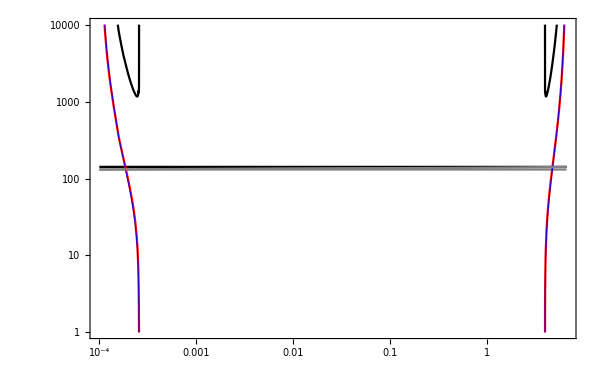

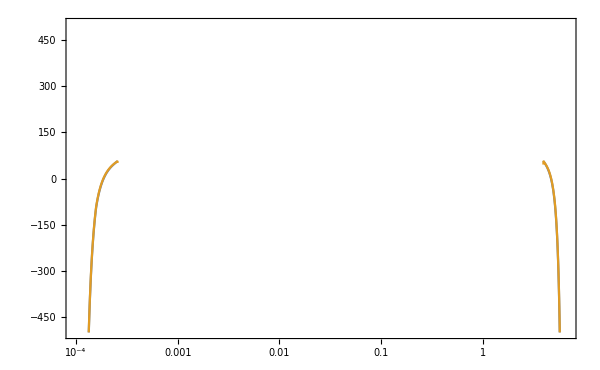

Plot::plln: Limiting value 6.10077×10^-12 Max[tptn0,tptw0] in {x,0.000099637556844028822859841490866,6.10077×10^-12 Max[tptn0,tptw0]} is not a machine-sized real number.

LogLinearPlot[{Log[4/3 π 1^3 x (tptn0 Hdec-x)^3]+Γnucl[pars,1,Tofx[x]/Tcr,1,False,True] Log[10]+4 Log[Tcr/Hdec],Log[4/3 π 1^3 x (tptw0 Hdec-x)^3]+Γnucl[pars,1,Tofx[x]/Tcr,1,True,True] Log[10]+4 Log[Tcr/Hdec]},{x,xC1,Max[tptn0,tptw0] Hdec},Frame→True,PlotRange→{-100,100},ImageSize→600,LabelStyle→16,FrameLabel→{MaTeX[(t-t_i)H_i,Magnification→2],MaTeX[\ln[J(x_{\rm PT},x')],Magnification→2]},PlotLabel→MaTeX[\text{Origin of Bubbles},Magnification→1.7],GridLines→{Join[{xC1},{xMAX}],None}]

Plot::plln: Limiting value 6.10077×10^-11 Max[tptn0,tptw0] in {x,0.000099637556844028822859841490866,6.10077×10^-11 Max[tptn0,tptw0]} is not a machine-sized real number.

LogLinearPlot[{Log[8 π 1^3]+Γnucl[pars,1,Tofx[x]/Tcr,1,False,True] Log[10]-4 Log[Abs[S1Rate[dlnTdt[x],pars,Tcr,Tofx[x]]]],Log[8 π 1^3]+Γnucl[pars,1,Tofx[x]/Tcr,1,True,True] Log[10]-4 Log[Abs[S1Rate[dlnTdt[x],pars,Tcr,Tofx[x]]]]},{x,xC1,10 (Max[tptn0,tptw0] Hdec)},Frame→True,PlotRange→{-100,100},ImageSize→600,LabelStyle→16,FrameLabel→{MaTeX[(t-t_i)H_i,Magnification→2],MaTeX[\ln[\mathrm{cond}(x)],Magnification→2]},PlotLabel→MaTeX[\text{1PT condition},Magnification→1.7],GridLines→{Join[{xC1},{xMAX}],None}]

Plot::plln: Limiting value 6.10077×10^-11 Max[tptn0,tptw0] in {x,0.000099637556844028822859841490866,6.10077×10^-11 Max[tptn0,tptw0]} is not a machine-sized real number.

LogLinearPlot[{Log[Abs[S1Rate[dlnTdt[x],pars,Tcr,Tofx[x]]]/Hdec],Log[(√Abs[S2Rate[dlnTdt[x],d2lnTdt2[x],pars,Tcr,Tofx[x]]])/Hdec]},{x,xC1,10 (Max[tptn0,tptw0] Hdec)},Frame→True,PlotRange→{-10,40},ImageSize→600,LabelStyle→16,FrameLabel→{MaTeX[(t-t_i)H_i,Magnification→2],MaTeX[\ln[\vert S^(n)(x)\vert^{1/n}],Magnification→2]},PlotLabel→MaTeX[\text{Action rates of change},Magnification→1.7],GridLines→{Join[{xC1},{xMAX}],None}]

Plot::plln: Limiting value 6.10077×10^-11 Max[tptn0,tptw0] in {x,0.000099637556844028822859841490866,6.10077×10^-11 Max[tptn0,tptw0]} is not a machine-sized real number.

LogLinearPlot[{1,Log[Abs[S1Rate[dlnTdt[x],pars,Tcr,Tofx[x]]]/(√Abs[S2Rate[dlnTdt[x],d2lnTdt2[x],pars,Tcr,Tofx[x]]])]},{x,xC1,10 (Max[tptn0,tptw0] Hdec)},Frame→True,PlotRange→{-10,20},ImageSize→600,LabelStyle→16,FrameLabel→{MaTeX[(t-t_i)H_i,Magnification→2],MaTeX[\ln[\vert S^(n)(x)\vert^{1/n}],Magnification→2]},PlotLabel→MaTeX[\text{Action rates of change},Magnification→1.7],GridLines→{Join[{xC1},{xMAX}],None}]

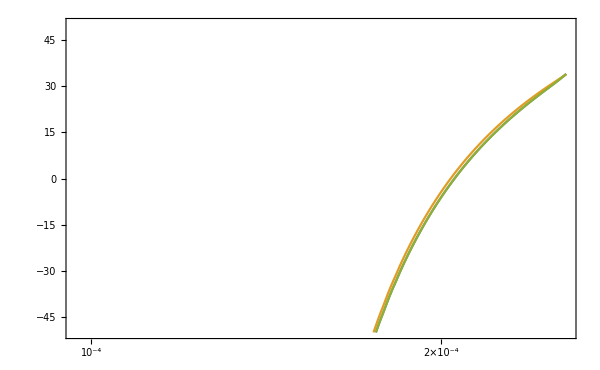

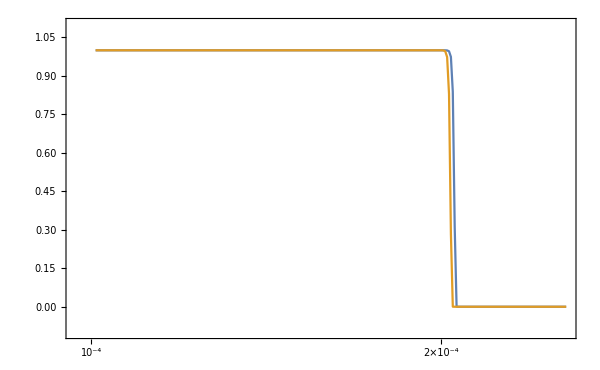

-Graphics-

```mathematica
DS=(Abs[S1Rate[dlnTdt[x],pars,Tcr,Tofx[x]]/dlnTdt[x]]);

LogLogPlot[{4Log[mpl/Tcr],4Log[Tcr/Hdec],SETemp[pars,Tcr,Tofx[x]],approxSE/.{θ->(Tofx[x]/Tcr)},SETemp[pars,Tcr,Tofx[xMAX]]+SE2Max*1/2(x-xMAX)^2*Hdec^-2,DS,4Log[Tofx[x]/Hofx[x]]},{x,xC1,xC2},Frame->True,PlotRange->{1,10^4},PlotStyle->{Black,Gray,Red,{Blue,Thickness[0.001]},Darker@Green},ImageSize->600,LabelStyle->16,FrameLabel->{MaTeX["(t-t_i)H_i",Magnification->2],MaTeX["S_\\mathrm{E}",Magnification->2]},PlotLabel->MaTeX["\\text{Euclidean Action}",Magnification->1.7],PlotLegends->Placed[LineLegend[{MaTeX["4 \\ln(m_\\mathrm{Pl}/T_\\mathrm{c})",Magnification->1],MaTeX["4 \\ln(T_\\mathrm{c}/H_\\mathrm{dec})",Magnification->1],MaTeX["S_E(x)",Magnification->1],MaTeX["S_E^\\mathrm{ appx.}(x)",Magnification->1],MaTeX["S_E^{\\prime\\prime}(t-t_\\mathrm{max})^2 /2",Magnification->1]}],{0.2,0.25}]]
(*Export[PlotsDir<>"SE_x.pdf",%]*)

LogLinearPlot[{Γnucl[pars,Tcr,Tofx[x],1,False,True]-4Log10[Hdec],Γnucl[pars,Tcr,Tofx[x],1,True,True]-4Log10[Hdec]},{x,xC1,xC2},Frame->True,PlotRange->{-500,500},ImageSize->600,LabelStyle->16,FrameLabel->{MaTeX["(t-t_i)H_i",Magnification->2],MaTeX["\\log_{10}(\\Gamma/\\mathcal{V}/H_\\mathrm{dec}^4)",Magnification->2]},PlotLegends->Placed[LineLegend[{MaTeX["\\text{w/o 0-modes}",Magnification->1.7],MaTeX["\\text{w/ 0-modes}",Magnification->1.7]}],{0.8,0.85}]]

LogLinearPlot[{Log[4/3 π*1^3(x)((tptn0*Hdec)-x)^3]+Γnucl[pars,1,Tofx[x]/Tcr,1,False,True]*Log[10]+4Log[Tcr/Hdec],Log[4/3 π*1^3(x)((tptw0*Hdec)-x)^3]+Γnucl[pars,1,Tofx[x]/Tcr,1,True,True]*Log[10]+4Log[Tcr/Hdec]},{x,xC1,(Max[tptn0,tptw0]*Hdec)},Frame->True,PlotRange->{-100,100},ImageSize->600,LabelStyle->16,FrameLabel->{MaTeX["(t-t_i)H_i",Magnification->2],MaTeX["\\ln[J(x_{\\rm PT},x')]",Magnification->2]},PlotLabel->MaTeX["\\text{Origin of Bubbles}",Magnification->1.7],GridLines->{{xC1}~Join~{xMAX },None}]

LogLinearPlot[{Log[8π*1^3]+Γnucl[pars,1,Tofx[x]/Tcr,1,False,True]*Log[10]-4Log[Abs[S1Rate[dlnTdt[x],pars,Tcr,Tofx[x]]]],Log[8π*1^3]+Γnucl[pars,1,Tofx[x]/Tcr,1,True,True]*Log[10]-4Log[Abs[S1Rate[dlnTdt[x],pars,Tcr,Tofx[x]]]]},{x,xC1,10((Max[tptn0,tptw0]*Hdec))},Frame->True,PlotRange->{-100,100},ImageSize->600,LabelStyle->16,FrameLabel->{MaTeX["(t-t_i)H_i",Magnification->2],MaTeX["\\ln[\\mathrm{cond}(x)]",Magnification->2]},PlotLabel->MaTeX["\\text{1PT condition}",Magnification->1.7],GridLines->{{xC1}~Join~{xMAX },None}]

LogLinearPlot[{Log[Abs[S1Rate[dlnTdt[x],pars,Tcr,Tofx[x]]]/Hdec],Log[√Abs[S2Rate[dlnTdt[x],d2lnTdt2[x],pars,Tcr,Tofx[x]]]/Hdec]},{x,xC1,10((Max[tptn0,tptw0]*Hdec))},Frame->True,PlotRange->{-10,40},ImageSize->600,LabelStyle->16,FrameLabel->{MaTeX["(t-t_i)H_i",Magnification->2],MaTeX["\\ln[\\vert S^(n)(x)\\vert^{1/n}]",Magnification->2]},PlotLabel->MaTeX["\\text{Action rates of change}",Magnification->1.7],GridLines->{{xC1}~Join~{xMAX },None}]

LogLinearPlot[{1,Log[Abs[S1Rate[dlnTdt[x],pars,Tcr,Tofx[x]]]/√Abs[S2Rate[dlnTdt[x],d2lnTdt2[x],pars,Tcr,Tofx[x]]]]},{x,xC1,10((Max[tptn0,tptw0]*Hdec))},Frame->True,PlotRange->{-10,20},ImageSize->600,LabelStyle->16,FrameLabel->{MaTeX["(t-t_i)H_i",Magnification->2],MaTeX["\\ln[\\vert S^(n)(x)\\vert^{1/n}]",Magnification->2]},PlotLabel->MaTeX["\\text{Action rates of change}",Magnification->1.7],GridLines->{{xC1}~Join~{xMAX},None}]


(*h(x) w/o scale factor*)
Lmlnh1=Lmlnh["hot",1,{Tofx,1/Hdec},pars,Tcr,1,False,{1,1},250];

(*Subscript[n, b](x) w/o scale factor*)
LnbLx=Lnbubble[Lmlnh1,{Tofx,1/Hdec},pars,Tcr,1,False,{1,1}];
xData=(InterpolatingFunctionCoordinates[LnbLx]//Flatten);
yData=(InterpolatingFunctionValuesOnGrid[LnbLx]//Flatten);
LnbLx={(10^xData),10^yData}//Transpose;

xData=(InterpolatingFunctionCoordinates[Lmlnh1]//Flatten);
yData=(InterpolatingFunctionValuesOnGrid[Lmlnh1]//Flatten);
Lmlnh1={(10^xData),yData}//Transpose;

Lmlnh2=Lmlnh["hot",1,{Tofx,1/Hdec},pars,Tcr,1,True,{1,1},250];

xData=(InterpolatingFunctionCoordinates[Lmlnh2]//Flatten);
yData=(InterpolatingFunctionValuesOnGrid[Lmlnh2]//Flatten);
Lmlnh2={(10^xData),yData}//Transpose;

Lmlnh3=Lmlnh["hot",1,{Tofx,1/Hdec},pars,Tcr,1,False,{1,1},500];
xData=(InterpolatingFunctionCoordinates[Lmlnh3]//Flatten);
yData=(InterpolatingFunctionValuesOnGrid[Lmlnh3]//Flatten);
Lmlnh3={(10^xData),yData}//Transpose;

ListLogLinearPlot[{Lmlnh1,Lmlnh2,Lmlnh3},Joined->True,PlotRange->{-50,50},Frame->True,ImageSize->600,LabelStyle->16,FrameLabel->{MaTeX["(t-t_i)H_i",Magnification->2],MaTeX["\\log_{10} (-\\ln h(x))",Magnification->2]},PlotLegends->Placed[LineLegend[{MaTeX["\\text{w/o 0-modes}",Magnification->1.2],MaTeX["\\text{w/ 0-modes}",Magnification->1.2],MaTeX["\\text{w/o 0-modes; more steps}",Magnification->1.2]}],{0.3,0.75}]]

Lmlnh1=({#⟦1⟧,Exp[-10^(#⟦2⟧)]}&/@Lmlnh1);
Lmlnh2=({#⟦1⟧,Exp[-10^(#⟦2⟧)]}&/@Lmlnh2);

ListLogLinearPlot[{Lmlnh1,Lmlnh2},Joined->True,PlotRange->{-0.1,1.1},Frame->True,ImageSize->600,LabelStyle->16,FrameLabel->{MaTeX["(t-t_i)H_i",Magnification->2],MaTeX["h(x)",Magnification->2]},PlotLegends->Placed[LineLegend[{MaTeX["\\text{w/o 0-modes}",Magnification->1.2],MaTeX["\\text{w/ 0-modes}",Magnification->1.2]}],{0.2,0.15}],GridLines->{{xMAX - 2/3}~Join~{tptn0*Hdec - 2/3}~Join~{tptw0*Hdec - 2/3},{1/E}}]

Lmlnh1=({#⟦1⟧,#⟦2⟧}&/@Lmlnh1);
Lmlnh2=({#⟦1⟧,#⟦2⟧}&/@Lmlnh2);

p1=ListLogLinearPlot[{Lmlnh1,Lmlnh2},Joined->True,PlotRange->{-0.1,1.1},Frame->True,ImageSize->600,LabelStyle->16,FrameLabel->{MaTeX["t H_i",Magnification->2],MaTeX["h(x)",Magnification->2]},PlotLegends->Placed[LineLegend[{MaTeX["\\text{w/o 0-modes}",Magnification->1.2],MaTeX["\\text{w/ 0-modes}",Magnification->1.2]}],{0.8,0.85}],GridLines->{{xMAX }~Join~{tptn0*Hdec}~Join~{tptw0*Hdec - 2/3},{1/E}}];
p2=LogLinearPlot[{Exp[-(4π)/3*(n0/Hdec^3)*1^3*(x-xMAX)^3],Exp[-(4π)/3*(n00m/Hdec^3)*1^3*(x-xMAX)^3]},{x,Lmlnh1⟦1,1⟧,Lmlnh1⟦-1,1⟧},PlotStyle->{Darker@Green,Red},PlotRange->{-0.1,1.1},PlotLegends->Placed[LineLegend[{MaTeX["\\text{w/o 0-modes; analytic, simultaneous}",Magnification->1.2],MaTeX["\\text{w 0-modes; analytic, simultaneous}",Magnification->1.2]}],{0.7,0.65}]];
Show[p1,p2]
```

#### SGWB

```mathematica
?gwSpectra
```

StringForm::string: String expected at position StandardForm[Short[Shallow[HoldForm[1], {10, 50}], 5]] in StandardForm[Short[Shallow[HoldForm[StringForm[fullResultLabels[[i]], ScientificForm[fullResult[[i]], 4]]], {10, 50}], 5]].

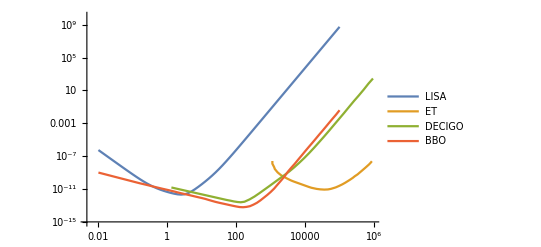

```mathematica
ListLogLogPlot[{{10^3#1,#2}&@@@GWLISASensitivity,{10^3#1,#2}&@@@GWETSensitivity,{10^3#1,#2}&@@@GWDECIGOSensitivity,{10^3#1,#2}&@@@GWBBOSensitivity},Joined->True,PlotLegends->{"LISA","ET","DECIGO","BBO"},PlotRange->{10^-15,10^10}]
```

*****************

No 0-modes:

.................

t_max=8.932*10^9
x_max=5.449*10^-2
T_max=3.53*10^3
t_c={1.633*10^7, 1.082*10^12}
x_c={9.964*10^-5, 6.599}
T_PT={1.199*10^3, 7.445*10^2}
t_PT={3.365*10^7, 2.017*10^12}
x_PT={2.053*10^-4, 1.23*10^1}
λ̄={1.101, 7.32*10^-1}
Φ_b={3.088*10^3, 2.665*10^3}
ϵ={6.228*10^11, 3.406*10^11}
E_c={9.122*10^4, 8.19*10^4}
S_E={7.611*10^1, 1.1*10^2}
S_E'={-1.422*10^-5, -1.956*10^-10}
S_E''={2.244*10^-12, 5.092*10^-22}
Γ/V={1.829*10^-21, 5.137*10^-37}
β_1={1.424*10^-5, 1.947*10^-10}
β_2={-2.245*10^-12, -5.088*10^-22}
n_b={8.073*10^-17, 1.6*10^-27}
R_b={2.314*10^5, 8.55*10^8}
⟨R⟩={1.712*10^7, 4.675*10^10}
β_eff={1.266*10^-5, 1.713*10^-10}
α_∞={1.009, 1.948}
α_n={1.381*10^-2, 9.275*10^-2}
κ_eff={7.207*10^1, -2.*10^1}
H_*={6.099*10^-12, 2.383*10^-13}
R={1.035*10^-2, 1.093}
Z={2.64*10^16, 5.193*10^15}

*****************

With 0-modes:

.................

t_max=8.932*10^9
x_max=5.449*10^-2
T_max=3.53*10^3
t_c={1.633*10^7, 1.082*10^12}
x_c={9.964*10^-5, 6.599}
T_PT={1.196*10^3, 7.482*10^2}
t_PT={3.34*10^7, 1.996*10^12}
x_PT={2.038*10^-4, 1.218*10^1}
λ̄={1.1, 7.38*10^-1}
Φ_b={3.09*10^3, 2.671*10^3}
ϵ={6.136*10^11, 3.385*10^11}
E_c={9.549*10^4, 8.546*10^4}
S_E={7.982*10^1, 1.142*10^2}
S_E'={-1.481*10^-5, -2.068*10^-10}
S_E''={2.389*10^-12, 5.503*10^-22}
Γ/V={2.007*10^-21, 6.085*10^-37}
β_1={1.456*10^-5, 2.031*10^-10}
β_2={-2.397*10^-12, -5.475*10^-22}
n_b={8.646*10^-17, 1.886*10^-27}
R_b={2.262*10^5, 8.093*10^8}
⟨R⟩={1.686*10^7, 4.57*10^10}
β_eff={1.295*10^-5, 1.81*10^-10}
α_∞={1.014, 1.937}
α_n={1.391*10^-2, 9.091*10^-2}
κ_eff={7.186*10^1, -2.03*10^1}
H_*={6.099*10^-12, 2.407*10^-13}
R={1.028*10^-2, 1.091}
Z={2.64*10^16, 5.219*10^15}

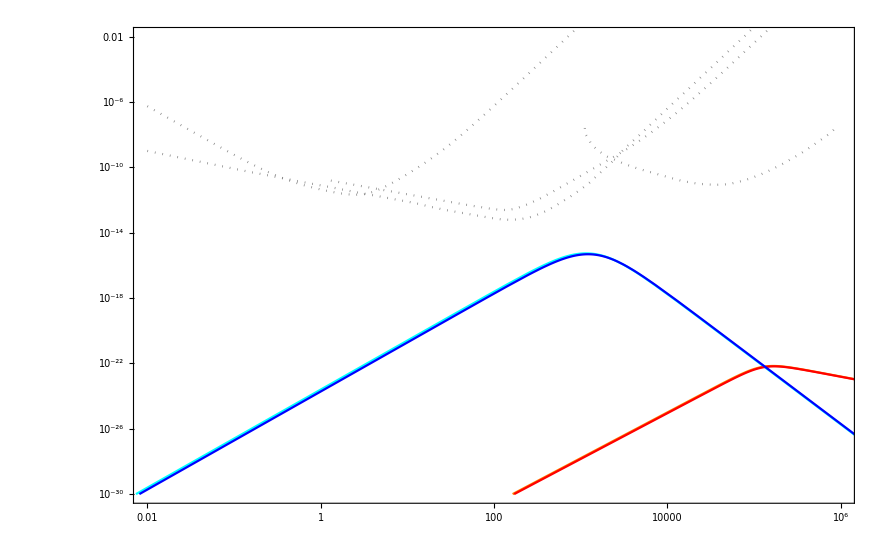

{(6.26035×10^-37 f^2.8)/(1+3.95999×10^-20 f^3.8),3.17794×10^-22 f^3 (1/(4+2.24005×10^-6 f^2))^(7/2),(5.57707×10^-37 f^2.8)/(1+3.63095×10^-20 f^3.8),2.42003×10^-22 f^3 (1/(4+2.02725×10^-6 f^2))^(7/2)}

```mathematica
(*gwSpectra[gUVs_List,vwCool_,coeffs_List,Tcrit_,Hd_,Γχ_,method_,verbose_:False,hh_:0.67,KfacΓfull_List:{1,False},NlxExpansionSum_List:{250,False,True},IRinstantVSRHwx_List:{Automatic,0,106.75,True,0},δxLargePrecAccu_List:{1/1000000,1000,30,20}]*)

IRs={Automatic,0,gSM,True,0};

Print["*****************"]
Print["No 0-modes:"]
Print["................."]
gwS=gwSpectra[{gDSUV,gVSUV},vwc,pars,Tcr,Hdec,Gam,"numeric",verbose,h,{1,False},{250,False,True},IRs,{10^-6,10^10,30,20}];
Print["*****************"]
Print["With 0-modes:"]
Print["................."]
gwS=gwS~Join~gwSpectra[{gDSUV,gVSUV},vwc,pars,Tcr,Hdec,Gam,"numeric",verbose,h,{1,True},{250,False,True},IRs,{10^-6,10^10,30,20}];

p1=LogLogPlot[gwS,{f,0.001,10^9},PlotStyle->{Orange,Cyan,Red,Blue},Frame->True,PlotRange->(*All*){{0.01,10^6},{(*10^-20*)10^-30,0.01}},PlotLegends->Placed[LineLegend[{MaTeX["\\text{Hot, w/o 0-modes}",Magnification->1.2],MaTeX["\\text{Cold, w/o 0-modes}",Magnification->1.2],MaTeX["\\text{Hot, w/ 0-modes}",Magnification->1.2],MaTeX["\\text{Cold, w/ 0-modes}",Magnification->1.2]}],{0.3,0.15}]];
p2=ListLogLogPlot[{{10^3#1,#2}&@@@GWLISASensitivity,{10^3#1,#2}&@@@GWETSensitivity,{10^3#1,#2}&@@@GWDECIGOSensitivity,{10^3#1,#2}&@@@GWBBOSensitivity},Joined->True,PlotStyle->{{Gray,Dotted}}];
Show[p1,p2]
(*Export[PlotsDir<>"sgwb.pdf",%]*)

gwS
```

```mathematica
"β_eff={1.266*10^-5, 1.713*10^-10}\\nα_∞={1.009, 1.948}\\nα_n={1.381*10^-2, 9.275*10^-2}\\nκ_eff={7.207*10^1, -2.*10^1}\\nH_*={6.099*10^-12, 2.383*10^-13}\\nR={1.035*10^-2, 1.093}\\nZ={2.64*10^16, 5.193*10^15}"
```

```mathematica
((1.266*10^-5)/(2.64*10^16))/((1.713*10^-10)/(5.193*10^15))
```

14537.5

```mathematica
(2.64*10^16)^(1/4)
```

12746.8

```mathematica
D[(6.260345946796685*^-37 f^2.8)/(1+3.9599869739933825*^-20 f^3.8),f]
NSolve[%==0,f,Reals]
```

-(9.42054×10^-56 f^5.6)/((1+3.95999×10^-20 f^3.8)^2)+(1.7529×10^-36 f^1.8)/(1+3.95999×10^-20 f^3.8)

{{f→0.},{f→167318.}}

```mathematica
(6.260345946796685*^-37 f^2.8)/(1+3.9599869739933825*^-20 f^3.8)/.{f->167318.21779097407}
```

6.96203×10^-23

```mathematica
Maximize[(6.260345946796685*^-37 f^2.8)/(1+3.9599869739933825*^-20 f^3.8),f]
```

NMaximize::nrnum: The function value 0.478616-0.347735 ⅈ is not a real number at {f} = {-0.829053}.

Maximize[(6.26035×10^-37 f^2.8)/(1+3.95999×10^-20 f^3.8),f]

## ***Scratch***